# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 30000/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
bBzSKA=bmeanzSKA+dbz/2;
bFzSKA=bmeanzSKA-dbz/2;
bTzSKA=(bBzSKA+bFzSKA)/2;
```

```mathematica
bBzSKA
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bB0=b1+db/2
bF0=b1-db/2
```

1.054

0.054

```mathematica
b1B=b1;
b1F=b1;
b2B=b2;
b2F=b2;
```

```mathematica
b1B
```

0.554

Import CAMB results

```mathematica
Length[zsigma]
```

100

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=zsigma[[All,2]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.814468

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.627151

```mathematica
sigma8z[0.5]
```

0.627168

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

Need of fevolB and fevolF

```mathematica
bBtildezSKA=bBzSKA D1zSKA Sigma8z0/D10
bFtildezSKA=bFzSKA D1zSKA Sigma8z0/D10
```

{0.845096,0.837813,0.832225,0.828564,0.826993,0.827618,0.830509,0.835711,0.843256,0.853172,0.865485,0.880225,0.897432,0.917153,0.939447,0.964384,0.992045,1.02253,1.05594}

{0.0925901,0.124044,0.154884,0.185276,0.2154,0.245446,0.275603,0.306056,0.336987,0.368571,0.400978,0.434376,0.468928,0.5048,0.542155,0.581158,0.62198,0.664792,0.709776}

```mathematica
bBtildezSKA-bFtildezSKA
```

{0.752505,0.713769,0.677341,0.643289,0.611593,0.582172,0.554906,0.529655,0.50627,0.484602,0.464507,0.44585,0.428504,0.412353,0.397292,0.383225,0.370065,0.357734,0.346161}

```mathematica
(bBtildezSKA+bFtildezSKA)/2
```

{0.468843,0.480929,0.493555,0.50692,0.521196,0.536532,0.553056,0.570883,0.590122,0.610871,0.633231,0.6573,0.68318,0.710977,0.740801,0.772771,0.807012,0.843659,0.882856}

# Multi-SPLIT Covariance

## Covariance Blocks

## Parameters

### Galaxy bias

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bT[m_,dbz_]:=bmeanzSKA ;
```

#### Standard splitting 50% (m = 2)

```mathematica
m = 2;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA50=bB[2, dbz]
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA50=bF[2,dbz]
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bTzSKA50 = bT[2,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA50 = 1/2;
```

```mathematica
smodelBzSKA50 = List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
```

```mathematica
fevolBzSKA50 = List[3.00956639,0.07976877,-0.81552783,-0.6173486,-0.39242556,-0.31155665,-0.26595514,-0.1091582,0.07791229,0.18253319,0.17336397,0.03980399,-0.12308668,-0.28681099,-0.41997146,-0.51728093,-0.57341237,-0.57764042,-0.55234844];
```

FAINT

```mathematica
nFSKA50 = 1/2;
```

```mathematica
smodelzSKA50 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA50);]
```

```mathematica
m
```

2

```mathematica
smodelFzSKA50 = (m/(m-1)) smodelzSKA50 -(1/(m-1)) smodelBzSKA50
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
fevolFzSKA50 = List[1.49669846,4.74321837,4.48561914,3.00325909,1.42466759,0.23953114,-0.63019961,-1.38888192,-2.01572455,-2.47043394,-2.7319998,-2.83059041,-2.87381247,-2.89939059,-2.94565432,-3.01777315,-3.12068025,-3.25274921,-3.36209773];
```

#### Splitting with 40% Bright (m=2.5)

```mathematica
m=2.5;
```

```mathematica
db=1.1;
dbz=Table[db,{i,Length[zSKA]}];
```

```mathematica
bBzSKA30=bB[2.5, dbz]
```

{1.28304,1.33379,1.38867,1.44801,1.51219,1.5816,1.65666,1.73784,1.82563,1.92056,2.02323,2.13426,2.25434,2.38419,2.52462,2.67649,2.84073,3.01834,3.21042}

```mathematica
bFzSKA30=bF[2.5,dbz]
```

{0.183042,0.233787,0.288665,0.348013,0.412194,0.481603,0.556665,0.63784,0.725627,0.820564,0.923233,1.03426,1.15434,1.28419,1.42462,1.57649,1.74073,1.91834,2.11042}

```mathematica
bTzSKA30 = bT[2.5,dbz]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

BRIGHT

```mathematica
nBSKA30 = 2/5;
```

```mathematica
smodelBzSKA30 = List[0.36074861,0.37136166,0.49125934,0.57258774,0.63507917,0.69611407,0.76565208,0.84126453,0.91598191,0.98606495,1.058817,1.13757212,1.22263581,1.31424594,1.41079416,1.51020605,1.61003934,1.7093556,1.80809726];
```

```mathematica
fevolBzSKA30 = List[2.73980215,0.87093286,-0.58533358,-0.68533239,-0.38434179,-0.1213791,-0.02064849,-0.00096973,0.04316954,0.14762866,0.23532289,0.26522591,0.25559428,0.19933758,0.12513341,0.05646589,0.01610228,0.01979882,0.05225069];
```

FAINT

```mathematica
nFSKA30 = 3/5;
```

```mathematica
smodelzSKA30 = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=3,m=1/(1-nFSKA30);]
m
```

5/2

```mathematica
smodelFzSKA30 = (m/(m-1)) smodelzSKA30 -(1/(m-1)) smodelBzSKA30
```

{-0.0717195,0.0323352,0.0823569,0.185643,0.315942,0.448423,0.568311,0.679587,0.788358,0.898427,1.00815,1.11545,1.22299,1.32911,1.43652,1.54656,1.66074,1.78001,1.89946}

```mathematica
fevolFzSKA30 = List[1.92868594,3.43853404,3.44863181,2.445147,1.11642955,0.02089814,-0.73302996,-1.24772028,-1.64362324,-2.00500307,-2.28907845,-2.50247262,-2.66781215,-2.7880597,-2.88811043,-2.98352232,-3.08914536,-3.20519057,-3.29687227];
```

### Survey

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
nBzSKA50=Table[nBSKA50, {i,Length[zSKA]}];
nFzSKA50=Table[nFSKA50, {i,Length[zSKA]}];
nBzSKA30=Table[nBSKA30, {i,Length[zSKA]}];
nFzSKA30=Table[nFSKA30, {i,Length[zSKA]}];
```

```mathematica
nBzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nFzSKA50
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nBzSKA30
```

{2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5}

```mathematica
nFzSKA30
```

{3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5,3/5}

```mathematica
NbarBzSKA50=NbarzSKA*nBzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarFzSKA50=NbarzSKA*nFzSKA50
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarBzSKA30=NbarzSKA*nBzSKA30
```

{0.0800674,0.0468782,0.0278944,0.0169175,0.0104217,0.0065991,0.00422291,0.00272487,0.00175632,0.00112353,0.000718024,0.000455868,0.000286693,0.000179506,0.000110416,0.0000671533,0.000040292,0.0000236328,0.0000135598}

```mathematica
NbarFzSKA30=NbarzSKA*nFzSKA30
```

{0.120101,0.0703173,0.0418417,0.0253762,0.0156325,0.00989865,0.00633436,0.00408731,0.00263448,0.00168529,0.00107704,0.000683801,0.000430039,0.000269259,0.000165623,0.00010073,0.000060438,0.0000354492,0.0000203397}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA50/nBzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffFSKA50=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA50/nFzSKA50
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffBSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA30/nBzSKA30
```

{2.1756×10^-8,1.36409×10^-8,1.18159×10^-8,1.19246×10^-8,1.31489×10^-8,1.51293×10^-8,1.81153×10^-8,2.2342×10^-8,2.84109×10^-8,3.7269×10^-8,4.98843×10^-8,6.82859×10^-8,9.56328×10^-8,1.36055×10^-7,1.98951×10^-7,2.96717×10^-7,4.5186×10^-7,7.0846×10^-7,1.14197×10^-6}

```mathematica
coeffFSKA30=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA30/nFzSKA30
```

{1.4504×10^-8,9.09394×10^-9,7.87729×10^-9,7.94976×10^-9,8.76592×10^-9,1.00862×10^-8,1.20768×10^-8,1.48946×10^-8,1.89406×10^-8,2.4846×10^-8,3.32562×10^-8,4.55239×10^-8,6.37552×10^-8,9.07032×10^-8,1.32634×10^-7,1.97811×10^-7,3.0124×10^-7,4.72307×10^-7,7.61313×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA50=(5smodelBzSKA50 +(2-5smodelBzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA50)fzSKA
```

{3.03044,1.96942,1.50533,1.08587,0.778835,0.633417,0.577577,0.500896,0.433983,0.449219,0.574176,0.83023,1.14574,1.49666,1.85103,2.19899,2.5307,2.83137,3.11887}

```mathematica
cFzSKA50=(5smodelFzSKA50 +(2-5smodelFzSKA50)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA50)fzSKA
```

{8.73219,3.49283,1.72274,1.11051,1.14024,1.34369,1.62634,2.0112,2.43762,2.84422,3.1753,3.42655,3.6648,3.91551,4.20934,4.55135,4.94709,5.39644,5.84627}

```mathematica
cBzSKA30=(5smodelBzSKA30 +(2-5smodelBzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA30)fzSKA
```

{0.548459,1.28548,1.16416,0.918292,0.624598,0.410284,0.330432,0.344564,0.383827,0.412782,0.4763,0.608277,0.796094,1.0492,1.34352,1.6569,1.96525,2.24986,2.52198}

```mathematica
cFzSKA30=(5smodelFzSKA30 +(2-5smodelFzSKA30)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA30)fzSKA
```

{9.43656,3.69489,1.91396,1.21812,1.18283,1.37407,1.61631,1.8637,2.13712,2.46934,2.80703,3.1418,3.47805,3.81068,4.15462,4.52069,4.92133,5.3566,5.78963}

### Elements

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
G[1,3,3,3]
```

24/385

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2corrCC[n,m]coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

4

```mathematica
4 i /. i -> 43
```

172

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

Monopole 50  - Monopole 50

```mathematica
coeffvarCCpop50pop30BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{6.38886×10^-9,2.56214×10^-9,1.43643×10^-9,9.54004×10^-10,7.02828×10^-10,5.56032×10^-10,4.63852×10^-10,4.03461×10^-10,3.6319×10^-10,3.36607×10^-10,3.19976×10^-10,3.11073×10^-10,3.0858×10^-10,3.11767×10^-10,3.20318×10^-10,3.34236×10^-10,3.53794×10^-10,3.79524×10^-10,4.1222×10^-10}

```mathematica
coeffvarCCpop30pop50BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{6.38886×10^-9,2.56214×10^-9,1.43643×10^-9,9.54004×10^-10,7.02828×10^-10,5.56032×10^-10,4.63852×10^-10,4.03461×10^-10,3.6319×10^-10,3.36607×10^-10,3.19976×10^-10,3.11073×10^-10,3.0858×10^-10,3.11767×10^-10,3.20318×10^-10,3.34236×10^-10,3.53794×10^-10,3.79524×10^-10,4.1222×10^-10}

```mathematica
coeffvarCCpop50pop30FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{7.22484×10^-11,4.15131×10^-11,3.14725×10^-11,2.70891×10^-11,2.50572×10^-11,2.43017×10^-11,2.44006×10^-11,2.51811×10^-11,2.65868×10^-11,2.86279×10^-11,3.13623×10^-11,3.48888×10^-11,3.93479×10^-11,4.49271×10^-11,5.18693×10^-11,6.04858×10^-11,7.11725×10^-11,8.44326×10^-11,1.00904×10^-10}

```mathematica
coeffvarCCpop30pop50FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{7.22484×10^-11,4.15131×10^-11,3.14725×10^-11,2.70891×10^-11,2.50572×10^-11,2.43017×10^-11,2.44006×10^-11,2.51811×10^-11,2.65868×10^-11,2.86279×10^-11,3.13623×10^-11,3.48888×10^-11,3.93479×10^-11,4.49271×10^-11,5.18693×10^-11,6.04858×10^-11,7.11725×10^-11,8.44326×10^-11,1.00904×10^-10}

```mathematica
varCCMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCCpop50pop30BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCCpop30pop50BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCCpop50pop30FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
varCCMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCCpop30pop50FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

```mathematica
coeffvarCCpop50BFpop30BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{5.92892×10^-10,2.91634×10^-10,1.93877×10^-10,1.48942×10^-10,1.24589×10^-10,1.10347×10^-10,1.01935×10^-10,9.73334×10^-11,9.5514×10^-11,9.5939×10^-11,9.83484×10^-11,1.02659×10^-10,1.08915×10^-10,1.17269×10^-10,1.27974×10^-10,1.4139×10^-10,1.57995×10^-10,1.78409×10^-10,2.03422×10^-10}

```mathematica
coeffvarCCpop30BFpop50BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{5.92892×10^-10,2.91634×10^-10,1.93877×10^-10,1.48942×10^-10,1.24589×10^-10,1.10347×10^-10,1.01935×10^-10,9.73334×10^-11,9.5514×10^-11,9.5939×10^-11,9.83484×10^-11,1.02659×10^-10,1.08915×10^-10,1.17269×10^-10,1.27974×10^-10,1.4139×10^-10,1.57995×10^-10,1.78409×10^-10,2.03422×10^-10}

```mathematica
varCCMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.88612×10^-9,8.4017×10^-10,5.14201×10^-10,3.68073×10^-10,2.8947×10^-10,2.42687×10^-10,2.13326×10^-10,1.94634×10^-10,1.83111×10^-10,1.76825×10^-10,1.74683×10^-10,1.76086×10^-10,1.80752×10^-10,1.88627×10^-10,1.99837×10^-10,2.14672×10^-10,2.33585×10^-10,2.57205×10^-10,2.86363×10^-10}

```mathematica
coeffvarCC30BFx50B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.88612×10^-9,8.4017×10^-10,5.14201×10^-10,3.68073×10^-10,2.8947×10^-10,2.42687×10^-10,2.13326×10^-10,1.94634×10^-10,1.83111×10^-10,1.76825×10^-10,1.74683×10^-10,1.76086×10^-10,1.80752×10^-10,1.88627×10^-10,1.99837×10^-10,2.14672×10^-10,2.33585×10^-10,2.57205×10^-10,2.86363×10^-10}

```mathematica
coeffvarCC50Fx30BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.01518×10^-10,1.07825×10^-10,7.69526×10^-11,6.28508×10^-11,5.5492×10^-11,5.15953×10^-11,4.98267×10^-11,4.95778×10^-11,5.05646×10^-11,5.26738×10^-11,5.58962×10^-11,6.02991×10^-11,6.60152×10^-11,7.32422×10^-11,8.22481×10^-11,9.33829×10^-11,1.07096×10^-10,1.23956×10^-10,1.44685×10^-10}

```mathematica
coeffvarCC30BFx50F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{2.01518×10^-10,1.07825×10^-10,7.69526×10^-11,6.28508×10^-11,5.5492×10^-11,5.15953×10^-11,4.98267×10^-11,4.95778×10^-11,5.05646×10^-11,5.26738×10^-11,5.58962×10^-11,6.02991×10^-11,6.60152×10^-11,7.32422×10^-11,8.22481×10^-11,9.33829×10^-11,1.07096×10^-10,1.23956×10^-10,1.44685×10^-10}

```mathematica
coeffvarCC30Bx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{1.81884×10^-9,8.23625×10^-10,5.09859×10^-10,3.67972×10^-10,2.91151×10^-10,2.45212×10^-10,2.16295×10^-10,1.97867×10^-10,1.86527×10^-10,1.80393×10^-10,1.78402×10^-10,1.79968×10^-10,1.84821×10^-10,1.92913×10^-10,2.04378×10^-10,2.19513×10^-10,2.38778×10^-10,2.6281×10^-10,2.92447×10^-10}

```mathematica
coeffvarCC50BFx30B00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.81884×10^-9,8.23625×10^-10,5.09859×10^-10,3.67972×10^-10,2.91151×10^-10,2.45212×10^-10,2.16295×10^-10,1.97867×10^-10,1.86527×10^-10,1.80393×10^-10,1.78402×10^-10,1.79968×10^-10,1.84821×10^-10,1.92913×10^-10,2.04378×10^-10,2.19513×10^-10,2.38778×10^-10,2.6281×10^-10,2.92447×10^-10}

```mathematica
coeffvarCC30Fx50BF00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.03931×10^-10,1.08186×10^-10,7.67273×10^-11,6.23711×10^-11,5.48681×10^-11,5.08696×10^-11,4.90149×10^-11,4.86828×10^-11,4.95823×10^-11,5.1595×10^-11,5.4708×10^-11,5.89852×10^-11,6.45559×10^-11,7.16139×10^-11,8.0423×10^-11,9.13285×10^-11,1.04773×10^-10,1.21321×10^-10,1.41685×10^-10}

```mathematica
coeffvarCC50BFx30F00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.03931×10^-10,1.08186×10^-10,7.67273×10^-11,6.23711×10^-11,5.48681×10^-11,5.08696×10^-11,4.90149×10^-11,4.86828×10^-11,4.95823×10^-11,5.1595×10^-11,5.4708×10^-11,5.89852×10^-11,6.45559×10^-11,7.16139×10^-11,8.0423×10^-11,9.13285×10^-11,1.04773×10^-10,1.21321×10^-10,1.41685×10^-10}

```mathematica
varCCMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONO50Fx30BFLp4d4to172zSKA= Table[coeffvarCC50Fx30BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30BFx50FLp4d4to172zSKA= Table[coeffvarCC30BFx50F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BFLp4d4to172zSKA= Table[coeffvarCC30Fx50BF00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50BFx30FLp4d4to172zSKA= Table[coeffvarCC50BFx30F00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{6.06134×10^-10,2.94703×10^-10,1.94287×10^-10,1.48335×10^-10,1.235×10^-10,1.08989×10^-10,1.00397×10^-10,9.56558×10^-11,9.37095×10^-11,9.40063×10^-11,9.62774×10^-11,1.00433×10^-10,1.06512×10^-10,1.14663×10^-10,1.25132×10^-10,1.38275×10^-10,1.54564×10^-10,1.7461×10^-10,1.99196×10^-10}

```mathematica
coeffvarCCpop30Fpop50BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{6.06134×10^-10,2.94703×10^-10,1.94287×10^-10,1.48335×10^-10,1.235×10^-10,1.08989×10^-10,1.00397×10^-10,9.56558×10^-11,9.37095×10^-11,9.40063×10^-11,9.62774×10^-11,1.00433×10^-10,1.06512×10^-10,1.14663×10^-10,1.25132×10^-10,1.38275×10^-10,1.54564×10^-10,1.7461×10^-10,1.99196×10^-10}

```mathematica
coeffvarCCpop50Fpop30BzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{5.81257×10^-10,2.88964×10^-10,1.9361×10^-10,1.49615×10^-10,1.25718×10^-10,1.11739×10^-10,1.03504×10^-10,9.9045×10^-11,9.73557×10^-11,9.79126×10^-11,1.00465×10^-10,1.04934×10^-10,1.11372×10^-10,1.19935×10^-10,1.3088×10^-10,1.44575×10^-10,1.61502×10^-10,1.8229×10^-10,2.07737×10^-10}

```mathematica
coeffvarCCpop30Bpop50FzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{5.81257×10^-10,2.88964×10^-10,1.9361×10^-10,1.49615×10^-10,1.25718×10^-10,1.11739×10^-10,1.03504×10^-10,9.9045×10^-11,9.73557×10^-11,9.79126×10^-11,1.00465×10^-10,1.04934×10^-10,1.11372×10^-10,1.19935×10^-10,1.3088×10^-10,1.44575×10^-10,1.61502×10^-10,1.8229×10^-10,2.07737×10^-10}

```mathematica
varCCMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCCpop50Bpop30FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCCpop30Fpop50BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCCpop30Bpop50FzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCCMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCCpop50Fpop30BzSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
coeffvarCC50BFx30BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{2.48171×10^-8,1.05333×10^-9,9.24082×10^-11,1.77635×10^-11,1.60729×10^-11,2.03428×10^-11,2.47103×10^-11,3.00862×10^-11,3.60241×10^-11,4.20359×10^-11,4.56518×10^-11,4.61741×10^-11,4.56727×10^-11,4.46556×10^-11,4.43319×10^-11,4.51495×10^-11,4.7648×10^-11,5.22677×10^-11,5.75743×10^-11}

```mathematica
coeffvarCC30BFx50BFrelzSKA=coeffvarCCrelSKAz[1,1,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{2.48171×10^-8,1.05333×10^-9,9.24082×10^-11,1.77635×10^-11,1.60729×10^-11,2.03428×10^-11,2.47103×10^-11,3.00862×10^-11,3.60241×10^-11,4.20359×10^-11,4.56518×10^-11,4.61741×10^-11,4.56727×10^-11,4.46556×10^-11,4.43319×10^-11,4.51495×10^-11,4.7648×10^-11,5.22677×10^-11,5.75743×10^-11}

```mathematica
varCCDIP50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCC50BFx30BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCC30BFx50BFrelzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

```mathematica
coeffvarCC22=coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCCpop50pop3022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.8167×10^-9,7.36442×10^-10,4.15501×10^-10,2.76658×10^-10,2.03685×10^-10,1.60608×10^-10,1.33244×10^-10,1.15048×10^-10,1.02657×10^-10,9.41972×10^-11,8.85713×10^-11,8.51119×10^-11,8.34107×10^-11,8.32255×10^-11,8.44282×10^-11,8.69762×10^-11,9.08964×10^-11,9.62792×10^-11,1.03277×10^-10}

```mathematica
coeffvarCCpop50pop3022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{3.63029×10^-11,2.01704×10^-11,1.4792×10^-11,1.23121×10^-11,1.10064×10^-11,1.03089×10^-11,9.98984×10^-12,9.94492×10^-12,1.01263×10^-11,1.0516×10^-11,1.11142×10^-11,1.19352×10^-11,1.30051×10^-11,1.43623×10^-11,1.60585×10^-11,1.81611×10^-11,2.07566×10^-11,2.3955×10^-11,2.78958×10^-11}

```mathematica
coeffvarCCpop30pop5022BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{1.8167×10^-9,7.36442×10^-10,4.15501×10^-10,2.76658×10^-10,2.03685×10^-10,1.60608×10^-10,1.33244×10^-10,1.15048×10^-10,1.02657×10^-10,9.41972×10^-11,8.85713×10^-11,8.51119×10^-11,8.34107×10^-11,8.32255×10^-11,8.44282×10^-11,8.69762×10^-11,9.08964×10^-11,9.62792×10^-11,1.03277×10^-10}

```mathematica
coeffvarCCpop30pop5022FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{3.63029×10^-11,2.01704×10^-11,1.4792×10^-11,1.23121×10^-11,1.10064×10^-11,1.03089×10^-11,9.98984×10^-12,9.94492×10^-12,1.01263×10^-11,1.0516×10^-11,1.11142×10^-11,1.19352×10^-11,1.30051×10^-11,1.43623×10^-11,1.60585×10^-11,1.81611×10^-11,2.07566×10^-11,2.3955×10^-11,2.78958×10^-11}

```mathematica
varCCQUAD50Bx30BLp4d4to172zSKA= Table[coeffvarCCpop50pop3022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50BLp4d4to172zSKA= Table[coeffvarCCpop30pop5022BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCCpop50pop3022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCCpop30pop5022FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCpop50Bpop30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.41178×10^-10,1.14772×10^-10,7.40477×10^-11,5.52936×10^-11,4.49927×10^-11,3.87784×10^-11,3.48663×10^-11,3.24107×10^-11,3.09704×10^-11,3.03029×10^-11,3.02743×10^-11,3.08163×10^-11,3.1905×10^-11,3.35499×10^-11,3.57892×10^-11,3.86885×10^-11,4.23421×10^-11,4.68766×10^-11,5.24564×10^-11}

```mathematica
coeffvarCCpop30Bpop50F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{2.40446×10^-10,1.15988×10^-10,7.55536×10^-11,5.68114×10^-11,4.64653×10^-11,4.02014×10^-11,3.625×10^-11,3.37693×10^-11,3.23193×10^-11,3.16573×10^-11,3.16493×10^-11,3.22272×10^-11,3.33673×10^-11,3.50801×10^-11,3.74048×10^-11,4.04087×10^-11,4.41882×10^-11,4.88723×10^-11,5.46287×10^-11}

```mathematica
coeffvarCCpop50Fpop30B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{2.40446×10^-10,1.15988×10^-10,7.55536×10^-11,5.68114×10^-11,4.64653×10^-11,4.02014×10^-11,3.625×10^-11,3.37693×10^-11,3.23193×10^-11,3.16573×10^-11,3.16493×10^-11,3.22272×10^-11,3.33673×10^-11,3.50801×10^-11,3.74048×10^-11,4.04087×10^-11,4.41882×10^-11,4.88723×10^-11,5.46287×10^-11}

```mathematica
coeffvarCCpop30Fpop50B22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{2.41178×10^-10,1.14772×10^-10,7.40477×10^-11,5.52936×10^-11,4.49927×10^-11,3.87784×10^-11,3.48663×10^-11,3.24107×10^-11,3.09704×10^-11,3.03029×10^-11,3.02743×10^-11,3.08163×10^-11,3.1905×10^-11,3.35499×10^-11,3.57892×10^-11,3.86885×10^-11,4.23421×10^-11,4.68766×10^-11,5.24564×10^-11}

```mathematica
varCCQUAD50Bx30FLp4d4to172zSKA= Table[coeffvarCCpop50Bpop30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Bx50FLp4d4to172zSKA= Table[coeffvarCCpop30Bpop50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUAD50Fx30BLp4d4to172zSKA= Table[coeffvarCCpop50Fpop30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BLp4d4to172zSKA= Table[coeffvarCCpop30Fpop50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC[2,2,bL,bM,bN,bP,f]
```

1/5 bL bM bN bP+11/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+3/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+17/231 (bL+bM+bN+bP) f^3+(83 f^4)/1287

```mathematica
coeffvarCCpop50BFpop30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.4069×10^-10,1.15344×10^-10,7.47833×10^-11,5.60411×10^-11,4.57199×10^-11,3.94819×10^-11,3.55505×10^-11,3.30826×10^-11,3.16374×10^-11,3.09726×10^-11,3.09541×10^-11,3.15138×10^-11,3.2628×10^-11,3.43065×10^-11,3.65881×10^-11,3.95392×10^-11,4.32553×10^-11,4.78641×10^-11,5.35315×10^-11}

```mathematica
coeffvarCCpop30BFpop50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{2.4069×10^-10,1.15344×10^-10,7.47833×10^-11,5.60411×10^-11,4.57199×10^-11,3.94819×10^-11,3.55505×10^-11,3.30826×10^-11,3.16374×10^-11,3.09726×10^-11,3.09541×10^-11,3.15138×10^-11,3.2628×10^-11,3.43065×10^-11,3.65881×10^-11,3.95392×10^-11,4.32553×10^-11,4.78641×10^-11,5.35315×10^-11}

```mathematica
varCCQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCCpop50BFpop30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCCpop30BFpop50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC50Bx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{6.44557×10^-10,2.84568×10^-10,1.72363×10^-10,1.21912×10^-10,9.45921×10^-11,7.81365×10^-11,6.75962×10^-11,6.06432×10^-11,5.60622×10^-11,5.3173×10^-11,5.15791×10^-11,5.1048×10^-11,5.14503×10^-11,5.27272×10^-11,5.48729×10^-11,5.79264×10^-11,6.19679×10^-11,6.71198×10^-11,7.35508×10^-11}

```mathematica
coeffvarCC30BFx50B22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{6.44557×10^-10,2.84568×10^-10,1.72363×10^-10,1.21912×10^-10,9.45921×10^-11,7.81365×10^-11,6.75962×10^-11,6.06432×10^-11,5.60622×10^-11,5.3173×10^-11,5.15791×10^-11,5.1048×10^-11,5.14503×10^-11,5.27272×10^-11,5.48729×10^-11,5.79264×10^-11,6.19679×10^-11,6.71198×10^-11,7.35508×10^-11}

```mathematica
coeffvarCC50Fx30BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{9.29502×10^-11,4.81154×10^-11,3.32566×10^-11,2.63139×10^-11,2.25055×10^-11,2.02654×10^-11,1.89499×10^-11,1.82555×10^-11,1.80282×10^-11,1.81896×10^-11,1.87045×10^-11,1.95661×10^-11,2.07894×10^-11,2.24078×10^-11,2.44732×10^-11,2.70575×10^-11,3.02554×10^-11,3.41885×10^-11,3.90119×10^-11}

```mathematica
coeffvarCC30BFx50F22zSKA =coeffCCSKA coeffvarCC[2,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{9.29502×10^-11,4.81154×10^-11,3.32566×10^-11,2.63139×10^-11,2.25055×10^-11,2.02654×10^-11,1.89499×10^-11,1.82555×10^-11,1.80282×10^-11,1.81896×10^-11,1.87045×10^-11,1.95661×10^-11,2.07894×10^-11,2.24078×10^-11,2.44732×10^-11,2.70575×10^-11,3.02554×10^-11,3.41885×10^-11,3.90119×10^-11}

```mathematica
varCCQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC30Bx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{6.38483×10^-10,2.84529×10^-10,1.73453×10^-10,1.23246×10^-10,9.59473×10^-11,7.94519×10^-11,6.88605×10^-11,6.18617×10^-11,5.72455×10^-11,5.43332×10^-11,5.27285×10^-11,5.21986×10^-11,5.26141×10^-11,5.39159×10^-11,5.60987×10^-11,5.92019×10^-11,6.33065×10^-11,6.85362×10^-11,7.50609×10^-11}

```mathematica
coeffvarCC50BFx30B22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{6.38483×10^-10,2.84529×10^-10,1.73453×10^-10,1.23246×10^-10,9.59473×10^-11,7.94519×10^-11,6.88605×10^-11,6.18617×10^-11,5.72455×10^-11,5.43332×10^-11,5.27285×10^-11,5.21986×10^-11,5.26141×10^-11,5.39159×10^-11,5.60987×10^-11,5.92019×10^-11,6.33065×10^-11,6.85362×10^-11,7.50609×10^-11}

```mathematica
coeffvarCC30Fx50BF22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{9.27785×10^-11,4.77382×10^-11,3.28577×10^-11,2.59202×10^-11,2.21202×10^-11,1.98861×10^-11,1.85727×10^-11,1.78761×10^-11,1.76422×10^-11,1.77923×10^-11,1.82911×10^-11,1.91316×10^-11,2.0328×10^-11,2.19135×10^-11,2.39392×10^-11,2.6476×10^-11,2.96176×10^-11,3.34844×10^-11,3.82296×10^-11}

```mathematica
coeffvarCC50BFx30F22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{9.27785×10^-11,4.77382×10^-11,3.28577×10^-11,2.59202×10^-11,2.21202×10^-11,1.98861×10^-11,1.85727×10^-11,1.78761×10^-11,1.76422×10^-11,1.77923×10^-11,1.82911×10^-11,1.91316×10^-11,2.0328×10^-11,2.19135×10^-11,2.39392×10^-11,2.6476×10^-11,2.96176×10^-11,3.34844×10^-11,3.82296×10^-11}

```mathematica
varCCQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.54682×10^-27,2.55583×10^-27,4.20156×10^-27,-1.66462×10^-27,-6.19934×10^-28,-4.8669×10^-28,-8.00794×10^-28,1.67482×10^-27,-1.11205×10^-27,1.00288×10^-27,-2.62226×10^-27,1.35927×10^-27,1.54028×10^-27,3.16014×10^-27,3.89895×10^-27,-2.48704×10^-27,-3.58611×10^-27,-5.56673×10^-27,-1.6061×10^-27}

```mathematica
coeffvarCCOCT50BFx30BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{9.41288×10^-9,3.96176×10^-10,3.42807×10^-11,6.54221×10^-12,6.01754×10^-12,7.69225×10^-12,9.37749×10^-12,1.14352×10^-11,1.36962×10^-11,1.59729×10^-11,1.73231×10^-11,1.74846×10^-11,1.72548×10^-11,1.683×10^-11,1.66705×10^-11,1.69443×10^-11,1.78526×10^-11,1.95581×10^-11,2.15186×10^-11}

```mathematica
coeffvarCCOCT30BFx50BFrelzSKA=coeffvarCCrelSKAz[3,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{9.41288×10^-9,3.96176×10^-10,3.42807×10^-11,6.54221×10^-12,6.01754×10^-12,7.69225×10^-12,9.37749×10^-12,1.14352×10^-11,1.36962×10^-11,1.59729×10^-11,1.73231×10^-11,1.74846×10^-11,1.72548×10^-11,1.683×10^-11,1.66705×10^-11,1.69443×10^-11,1.78526×10^-11,1.95581×10^-11,2.15186×10^-11}

```mathematica
varCCOCT50BFx30BFrelLp4d4to172zSKA=Table[coeffvarCCOCT50BFx30BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCOCT30BFx50BFrelLp4d4to172zSKA=Table[coeffvarCCOCT30BFx50BFrelzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

We use the HEXADECAPOLE of the TOTAL POPULATION (for each splitting, same total population)

```mathematica
bTzSKA50
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
bTzSKA30
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC[4,4,bT,bT,bQ,bQ,f]
```

(bQ^2 bT^2)/9+26/231 bQ bT (bQ+bT) f+(643 (bQ^2+4 bQ bT+bT^2) f^2)/15015+(218 (bQ+bT) f^3)/3003+(79 f^4)/2431

```mathematica
coeffvarCC50Tx30T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
coeffvarCC30Tx50T44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA30,bTzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCC50Tx30T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCC30Tx50T44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

```mathematica
coeffvarCC02[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC50Bx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-7.76705×10^-9,-3.21147×10^-9,-1.83238×10^-9,-1.22549×10^-9,-9.01219×10^-10,-7.06498×10^-10,-5.80371×10^-10,-4.94426×10^-10,-4.33872×10^-10,-3.9036×10^-10,-3.58882×10^-10,-3.36295×10^-10,-3.20563×10^-10,-3.10339×10^-10,-3.04732×10^-10,-3.03161×10^-10,-3.05269×10^-10,-3.10871×10^-10,-3.19918×10^-10}

```mathematica
coeffvarCC30Bx50B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-7.76705×10^-9,-3.21147×10^-9,-1.83238×10^-9,-1.22549×10^-9,-9.01219×10^-10,-7.06498×10^-10,-5.80371×10^-10,-4.94426×10^-10,-4.33872×10^-10,-3.9036×10^-10,-3.58882×10^-10,-3.36295×10^-10,-3.20563×10^-10,-3.10339×10^-10,-3.04732×10^-10,-3.03161×10^-10,-3.05269×10^-10,-3.10871×10^-10,-3.19918×10^-10}

```mathematica
coeffvarCC50Fx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.32362×10^-10,-1.29006×10^-10,-9.43248×10^-11,-7.80968×10^-11,-6.92744×10^-11,-6.42092×10^-11,-6.13944×10^-11,-6.01173×10^-11,-6.00132×10^-11,-6.08913×10^-11,-6.26588×10^-11,-6.52839×10^-11,-6.87784×10^-11,-7.31884×10^-11,-7.85906×10^-11,-8.50912×10^-11,-9.28272×10^-11,-1.01969×10^-10,-1.12726×10^-10}

```mathematica
coeffvarCC30Fx50F02zSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-2.32362×10^-10,-1.29006×10^-10,-9.43248×10^-11,-7.80968×10^-11,-6.92744×10^-11,-6.42092×10^-11,-6.13944×10^-11,-6.01173×10^-11,-6.00132×10^-11,-6.08913×10^-11,-6.26588×10^-11,-6.52839×10^-11,-6.87784×10^-11,-7.31884×10^-11,-7.85906×10^-11,-8.50912×10^-11,-9.28272×10^-11,-1.01969×10^-10,-1.12726×10^-10}

```mathematica
varCCMONO50BxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50Bx30B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30Bx50B02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50Fx30F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30Fx50F02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC0250Bx30F=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.4907×10^-9,-6.99815×10^-10,-4.4505×10^-10,-3.27172×10^-10,-2.61669×10^-10,-2.21256×10^-10,-1.94764×10^-10,-1.76858×10^-10,-1.64703×10^-10,-1.56682×10^-10,-1.51819×10^-10,-1.49514×10^-10,-1.49399×10^-10,-1.51257×10^-10,-1.54982×10^-10,-1.60551×10^-10,-1.68009×10^-10,-1.77463×10^-10,-1.8908×10^-10}

```mathematica
coeffvarCC0230Fx50B=coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-1.4907×10^-9,-6.99815×10^-10,-4.4505×10^-10,-3.27172×10^-10,-2.61669×10^-10,-2.21256×10^-10,-1.94764×10^-10,-1.76858×10^-10,-1.64703×10^-10,-1.56682×10^-10,-1.51819×10^-10,-1.49514×10^-10,-1.49399×10^-10,-1.51257×10^-10,-1.54982×10^-10,-1.60551×10^-10,-1.68009×10^-10,-1.77463×10^-10,-1.8908×10^-10}

```mathematica
coeffvarCC0230Bx50F=coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-1.5219×10^-9,-7.22402×10^-10,-4.62698×10^-10,-3.41728×10^-10,-2.74129×10^-10,-2.32222×10^-10,-2.04627×10^-10,-1.8589×10^-10,-1.73105×10^-10,-1.64604×10^-10,-1.5938×10^-10,-1.56809×10^-10,-1.56507×10^-10,-1.58247×10^-10,-1.61913×10^-10,-1.67476×10^-10,-1.74978×10^-10,-1.84522×10^-10,-1.96273×10^-10}

```mathematica
coeffvarCC0250Fx30B=coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.5219×10^-9,-7.22402×10^-10,-4.62698×10^-10,-3.41728×10^-10,-2.74129×10^-10,-2.32222×10^-10,-2.04627×10^-10,-1.8589×10^-10,-1.73105×10^-10,-1.64604×10^-10,-1.5938×10^-10,-1.56809×10^-10,-1.56507×10^-10,-1.58247×10^-10,-1.61913×10^-10,-1.67476×10^-10,-1.74978×10^-10,-1.84522×10^-10,-1.96273×10^-10}

```mathematica
varCCMONO50BxQUAD30FLp4d4to172zSKA=Table[coeffvarCC0250Bx30F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BLp4d4to172zSKA=Table[coeffvarCC0230Fx50B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50FLp4d4to172zSKA=Table[coeffvarCC0230Bx50F[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BLp4d4to172zSKA=Table[coeffvarCC0250Fx30B[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,bL,bM,bN,bP,f]
```

-5 (2/15 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+4/35 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+2/21 (bL+bM+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC50BFx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.5076×10^-9,-7.11419×10^-10,-4.53949×10^-10,-3.34447×10^-10,-2.67865×10^-10,-2.26694×10^-10,-1.99646×10^-10,-1.81324×10^-10,-1.68856×10^-10,-1.60596×10^-10,-1.55554×10^-10,-1.53119×10^-10,-1.52912×10^-10,-1.54712×10^-10,-1.5841×10^-10,-1.63977×10^-10,-1.71458×10^-10,-1.80958×10^-10,-1.92643×10^-10}

```mathematica
coeffvarCC30BFx50BF02zSKA = coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-1.5076×10^-9,-7.11419×10^-10,-4.53949×10^-10,-3.34447×10^-10,-2.67865×10^-10,-2.26694×10^-10,-1.99646×10^-10,-1.81324×10^-10,-1.68856×10^-10,-1.60596×10^-10,-1.55554×10^-10,-1.53119×10^-10,-1.52912×10^-10,-1.54712×10^-10,-1.5841×10^-10,-1.63977×10^-10,-1.71458×10^-10,-1.80958×10^-10,-1.92643×10^-10}

```mathematica
varCCMONO50BFxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]
```

-5 (2/15 bL (2 bN bP+bL (bN+bP)) f+4/35 (bL^2+bN bP+2 bL (bN+bP)) f^2+2/21 (2 bL+bN+bP) f^3+(8 f^4)/99)

```mathematica
coeffvarCC[0,2,bL,bL,bN,bP,f]-coeffvarCC[0,2,bN,bP,bL,bL,f]
```

0

```mathematica
coeffvarCC[0,2,bN,bN,bL,bM,f]
```

-5 (2/15 bN (bM bN+bL (2 bM+bN)) f+4/35 (bN (2 bM+bN)+bL (bM+2 bN)) f^2+2/21 (bL+bM+2 bN) f^3+(8 f^4)/99)

```mathematica
Collect[coeffvarCC[0,2,bL,bL,bN,bP,f] - coeffvarCC[0,2,bN,bN,bL,bM,f],f]
```

(2/3 bN (bM bN+bL (2 bM+bN))-2/3 bL (2 bN bP+bL (bN+bP))) f+(4/7 (bN (2 bM+bN)+bL (bM+2 bN))-4/7 (bL^2+bN bP+2 bL (bN+bP))) f^2+(10/21 (bL+bM+2 bN)-10/21 (2 bL+bN+bP)) f^3

```mathematica
coeffvarCC50Bx30BF02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-3.61822×10^-9,-1.57579×10^-9,-9.41131×10^-10,-6.55598×10^-10,-5.00204×10^-10,-4.0556×10^-10,-3.43695×10^-10,-3.01428×10^-10,-2.71829×10^-10,-2.50955×10^-10,-2.36432×10^-10,-2.26768×10^-10,-2.21009×10^-10,-2.18538×10^-10,-2.18971×10^-10,-2.22086×10^-10,-2.27785×10^-10,-2.36071×10^-10,-2.47036×10^-10}

```mathematica
coeffvarCC30BFx50B02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bBzSKA50,bBzSKA50,fzSKA]
```

{-3.61822×10^-9,-1.57579×10^-9,-9.41131×10^-10,-6.55598×10^-10,-5.00204×10^-10,-4.0556×10^-10,-3.43695×10^-10,-3.01428×10^-10,-2.71829×10^-10,-2.50955×10^-10,-2.36432×10^-10,-2.26768×10^-10,-2.21009×10^-10,-2.18538×10^-10,-2.18971×10^-10,-2.22086×10^-10,-2.27785×10^-10,-2.36071×10^-10,-2.47036×10^-10}

```mathematica
coeffvarCC30Bx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bBzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-3.71266×10^-9,-1.61851×10^-9,-9.67167×10^-10,-6.73886×10^-10,-5.14155×10^-10,-4.16797×10^-10,-3.53107×10^-10,-3.09552×10^-10,-2.79013×10^-10,-2.57438×10^-10,-2.42382×10^-10,-2.32314×10^-10,-2.26246×10^-10,-2.23543×10^-10,-2.23805×10^-10,-2.26802×10^-10,-2.32426×10^-10,-2.40678×10^-10,-2.51643×10^-10}

```mathematica
coeffvarCC50BFx30B02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-3.71266×10^-9,-1.61851×10^-9,-9.67167×10^-10,-6.73886×10^-10,-5.14155×10^-10,-4.16797×10^-10,-3.53107×10^-10,-3.09552×10^-10,-2.79013×10^-10,-2.57438×10^-10,-2.42382×10^-10,-2.32314×10^-10,-2.26246×10^-10,-2.23543×10^-10,-2.23805×10^-10,-2.26802×10^-10,-2.32426×10^-10,-2.40678×10^-10,-2.51643×10^-10}

```mathematica
coeffvarCC50BFx30F02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-5.93594×10^-10,-3.03153×10^-10,-2.06737×10^-10,-1.61275×10^-10,-1.35811×10^-10,-1.20196×10^-10,-1.10232×10^-10,-1.03902×10^-10,-1.00137×10^-10,-9.83341×10^-11,-9.8144×10^-11,-9.93679×10^-11,-1.01905×10^-10,-1.05724×10^-10,-1.10848×10^-10,-1.17346×10^-10,-1.25329×10^-10,-1.34951×10^-10,-1.46411×10^-10}

```mathematica
coeffvarCC30Fx50BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,fzSKA]
```

{-5.93594×10^-10,-3.03153×10^-10,-2.06737×10^-10,-1.61275×10^-10,-1.35811×10^-10,-1.20196×10^-10,-1.10232×10^-10,-1.03902×10^-10,-1.00137×10^-10,-9.83341×10^-11,-9.8144×10^-11,-9.93679×10^-11,-1.01905×10^-10,-1.05724×10^-10,-1.10848×10^-10,-1.17346×10^-10,-1.25329×10^-10,-1.34951×10^-10,-1.46411×10^-10}

```mathematica
coeffvarCC50Fx30BF02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-5.96739×10^-10,-3.06735×10^-10,-2.10091×10^-10,-1.64379×10^-10,-1.38707×10^-10,-1.22928×10^-10,-1.12837×10^-10,-1.06412×10^-10,-1.0258×10^-10,-1.00733×10^-10,-1.0052×10^-10,-1.01739×10^-10,-1.04288×10^-10,-1.08135×10^-10,-1.13303×10^-10,-1.1986×10^-10,-1.27917×10^-10,-1.37629×10^-10,-1.49194×10^-10}

```mathematica
coeffvarCC30BFx50F02zSKA= coeffCCSKA coeffvarCC[0,2,bBzSKA30,bFzSKA30,bFzSKA50,bFzSKA50,fzSKA]
```

{-5.96739×10^-10,-3.06735×10^-10,-2.10091×10^-10,-1.64379×10^-10,-1.38707×10^-10,-1.22928×10^-10,-1.12837×10^-10,-1.06412×10^-10,-1.0258×10^-10,-1.00733×10^-10,-1.0052×10^-10,-1.01739×10^-10,-1.04288×10^-10,-1.08135×10^-10,-1.13303×10^-10,-1.1986×10^-10,-1.27917×10^-10,-1.37629×10^-10,-1.49194×10^-10}

```mathematica
varCCMONO50BxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Bx30BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxQUAD30BFLp4d4to172zSKA=Table[coeffvarCC50Fx30BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30BLp4d4to172zSKA=Table[coeffvarCC50BFx30B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50BFxQUAD30FLp4d4to172zSKA=Table[coeffvarCC50BFx30F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Bx50BF02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxQUAD50BFLp4d4to172zSKA=Table[coeffvarCC30Fx50BF02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50BLp4d4to172zSKA=Table[coeffvarCC30BFx50B02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxQUAD50FLp4d4to172zSKA=Table[coeffvarCC30BFx50F02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC04[bL_,bM_,bN_,bP_,f_]=coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC50Bx30T04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC30Bx50T04BzSKA = coeffCCSKA coeffvarCC[0,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.12636×10^-9,4.90224×10^-10,2.90189×10^-10,1.98969×10^-10,1.48541×10^-10,1.17248×10^-10,9.63075×10^-11,8.15521×10^-11,7.07676×10^-11,6.26767×10^-11,5.64942×10^-11,5.17129×10^-11,4.79923×10^-11,4.50966×10^-11,4.28586×10^-11,4.11578×10^-11,3.99057×10^-11,3.90377×10^-11,3.85058×10^-11}

```mathematica
coeffvarCC50Fx30T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
coeffvarCC30Fx50T04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{3.47764×10^-10,1.65787×10^-10,1.06154×10^-10,7.79762×10^-11,6.18992×10^-11,5.1645×10^-11,4.46274×10^-11,3.96001×10^-11,3.58916×10^-11,3.3109×10^-11,3.10069×10^-11,2.94252×10^-11,2.82548×10^-11,2.742×10^-11,2.68672×10^-11,2.65578×10^-11,2.64648×10^-11,2.65688×10^-11,2.68573×10^-11}

```mathematica
varCCMONO50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC2pop04=coeffvarCC[0,4,bB,bF,bT,bT,f]
```

9 (8/315 (bT (2 bF+bT)+bB (bF+2 bT)) f^2+8/231 (bB+bF+2 bT) f^3+(16 f^4)/429)

```mathematica
coeffvarCC50BFx30T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
coeffvarCC30BFx50T04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{6.60844×10^-10,2.98554×10^-10,1.82618×10^-10,1.28923×10^-10,9.88188×10^-11,7.99013×10^-11,6.71062×10^-11,5.80127×10^-11,5.13268×10^-11,4.62969×10^-11,4.24577×10^-11,3.95068×10^-11,3.72401×10^-11,3.55157×10^-11,3.42326×10^-11,3.33183×10^-11,3.27199×10^-11,3.2399×10^-11,3.23282×10^-11}

```mathematica
varCCMONO50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCMONO30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50Bx30T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC50Fx30T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
coeffvarCC30Bx50T24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA30,bBzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-1.23886×10^-8,-5.32667×10^-9,-3.14353×10^-9,-2.16497×10^-9,-1.63366×10^-9,-1.31032×10^-9,-1.09873×10^-9,-9.53622×10^-10,-8.51234×10^-10,-7.7804×10^-10,-7.2588×10^-10,-6.89613×10^-10,-6.65914×10^-10,-6.52605×10^-10,-6.48277×10^-10,-6.52061×10^-10,-6.63488×10^-10,-6.82406×10^-10,-7.08927×10^-10}

```mathematica
coeffvarCC30Fx50T24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-2.42303×10^-9,-1.18442×10^-9,-7.79217×10^-10,-5.89527×10^-10,-4.83268×10^-10,-4.17499×10^-10,-3.74551×10^-10,-3.45955×10^-10,-3.27208×10^-10,-3.15744×10^-10,-3.10033×10^-10,-3.09156×10^-10,-3.12577×10^-10,-3.20027×10^-10,-3.31425×10^-10,-3.46852×10^-10,-3.66522×10^-10,-3.90779×10^-10,-4.20096×10^-10}

```mathematica
varCCQUAD50BxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Bx30T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD50FxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50Fx30T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Bx50T24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30FxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30Fx50T24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC2pop24=coeffvarCC[2,4,bB,bF,bT,bT,f]
```

-45 (4/105 bT (bF bT+bB (2 bF+bT)) f+(136 (bT (2 bF+bT)+bB (bF+2 bT)) f^2)/3465+(116 (bB+bF+2 bT) f^3)/3003+(16 f^4)/429)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC50BFx30T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
coeffvarCC30BFx50T24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{-5.64694×10^-9,-2.57595×10^-9,-1.59917×10^-9,-1.15107×10^-9,-9.03275×10^-10,-7.50513×10^-10,-6.49929×10^-10,-5.81138×10^-10,-5.33342×10^-10,-5.0036×10^-10,-4.78454×10^-10,-4.65291×10^-10,-4.59392×10^-10,-4.5984×10^-10,-4.66102×10^-10,-4.77935×10^-10,-4.95321×10^-10,-5.18437×10^-10,-5.47637×10^-10}

```mathematica
varCCQUAD50BFxHEXA30Lp4d4to172zSKA=Table[coeffvarCC50BFx30T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCQUAD30BFxHEXA50Lp4d4to172zSKA=Table[coeffvarCC30BFx50T24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2

```mathematica
coeffvarCC50BFx30BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,cBzSKA50,cFzSKA50,cBzSKA30,cFzSKA30,fzSKA]
```

{-1.85186×10^-7,-7.54545×10^-9,-6.1467×10^-10,-1.13108×10^-10,-1.12421×10^-10,-1.49597×10^-10,-1.84838×10^-10,-2.26655×10^-10,-2.7177×10^-10,-3.16313×10^-10,-3.41335×10^-10,-3.41854×10^-10,-3.34403×10^-10,-3.23117×10^-10,-3.17178×10^-10,-3.19767×10^-10,-3.34583×10^-10,-3.64512×10^-10,-3.99004×10^-10}

```mathematica
coeffvarCC30BFx50BF13zSKA= coeffvarCCrelSKAz [1,3,bBzSKA30,bFzSKA30,bBzSKA50,bFzSKA50,cBzSKA30,cFzSKA30,cBzSKA50,cFzSKA50,fzSKA]
```

{-1.85186×10^-7,-7.54545×10^-9,-6.1467×10^-10,-1.13108×10^-10,-1.12421×10^-10,-1.49597×10^-10,-1.84838×10^-10,-2.26655×10^-10,-2.7177×10^-10,-3.16313×10^-10,-3.41335×10^-10,-3.41854×10^-10,-3.34403×10^-10,-3.23117×10^-10,-3.17178×10^-10,-3.19767×10^-10,-3.34583×10^-10,-3.64512×10^-10,-3.99004×10^-10}

```mathematica
varCCDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCC50BFx30BF13zSKA[[k]]  varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCCDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCC30BFx50BF13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
coeffvarmixedJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
((oMP alpha0[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha0[bM, bN,f] ) /nP 
+((-1)^m oMN alpha0[bL,bP,f]  + (-1)^(n+m) oLN alpha0[bM,bP,f])/nN ) G[n,m,0,0] 
+ ((oMP alpha2[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha2[bM, bN,f] ) /nP 
+((-1)^m oMN alpha2[bL,bP,f]  + (-1)^(n+m) oLN alpha2[bM,bP,f])/nN )  G[n,m,2,0] 
+ ((oMP alpha4[bL, bN,f]  +  (-1)^m(-1)^(n+m)oLP alpha4[bM, bN,f] ) /nP 
+((-1)^m oMN alpha4[bL,bP,f]  + (-1)^(n+m) oLN alpha4[bM,bP,f])/nN ) G[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
2(alpha0[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha0[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nP G[n,m,0,0] 
+ 2(alpha2[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha2[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,2,0] 
+ 2(alpha4[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha4[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
4(alpha0[bL,bP,f] oLP )/nP G[n,m,0,0] + 4(alpha2[bL,bP,f] oLP )/nP G[n,m,2,0] + 4(alpha4[bL,bP,f] oLP)/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJoint[n_,m_,nN_,nP_,oLN_,oLP_,oMN_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJoint[n,m,nN,nP,oLN,oLP,oMN,oMP,bL,bM,bN,bP,f]
coeffvarCPgeneralJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexa[n,m,nN,nP,oLP,oMP,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPgeneralJointHexaHexa[n_,m_,nN_,nP_,oLP_,bL_,bM_,bN_,bP_,f_]:=
corrCP[n,m]coeffvarmixedJointHexaHexa[n,m,nN,nP,oLP,bL,bM,bN,bP,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

JOINT ANALYSIS 50X50 - 10X90

```mathematica
OBb = 4/5;
OBf = 1/5;
OFb = 0;
OFf = 1.0;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

```mathematica
OBt=1.0;
OFt=1.0;
```

```mathematica
OTt = 1.0;
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCPgeneral[0,0,n,n,b,b,b,b,f]
```

b^2/n+(2 b f)/(3 n)+f^2/(5 n)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nb,oBb,oBb,oBb,oBb,b,b,b,b,f]
```

(b^2 oBb)/nb+(2 b f oBb)/(3 nb)+(f^2 oBb)/(5 nb)

```mathematica
coeffvarCP50Bx30B00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{3.48674×10^-8,2.40381×10^-8,2.28541×10^-8,2.52841×10^-8,3.05435×10^-8,3.84989×10^-8,5.05199×10^-8,6.83459×10^-8,9.54536×10^-8,1.37737×10^-7,2.0316×10^-7,3.0707×10^-7,4.75843×10^-7,7.50725×10^-7,1.22014×10^-6,2.0272×10^-6,3.44709×10^-6,6.04857×10^-6,0.0000109361}

```mathematica
coeffvarCP50Fx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.30275×10^-9,1.97183×10^-9,2.25147×10^-9,2.91781×10^-9,4.05168×10^-9,5.78517×10^-9,8.50049×10^-9,1.2756×10^-8,1.96069×10^-8,3.09293×10^-8,4.95821×10^-8,8.10268×10^-8,1.35117×10^-7,2.284×10^-7,3.96136×10^-7,6.99697×10^-7,1.26037×10^-6,2.33488×10^-6,4.44277×10^-6}

```mathematica
coeffvarCP30Bx50B00zSKA=  coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb ,OBb ,OBb ,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{3.48674×10^-8,2.40381×10^-8,2.28541×10^-8,2.52841×10^-8,3.05435×10^-8,3.84989×10^-8,5.05199×10^-8,6.83459×10^-8,9.54536×10^-8,1.37737×10^-7,2.0316×10^-7,3.0707×10^-7,4.75843×10^-7,7.50725×10^-7,1.22014×10^-6,2.0272×10^-6,3.44709×10^-6,6.04857×10^-6,0.0000109361}

```mathematica
coeffvarCP30Fx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OFf,OFf ,OFf,OFf ,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{2.30275×10^-9,1.97183×10^-9,2.25147×10^-9,2.91781×10^-9,4.05168×10^-9,5.78517×10^-9,8.50049×10^-9,1.2756×10^-8,1.96069×10^-8,3.09293×10^-8,4.95821×10^-8,8.10268×10^-8,1.35117×10^-7,2.284×10^-7,3.96136×10^-7,6.99697×10^-7,1.26037×10^-6,2.33488×10^-6,4.44277×10^-6}

```mathematica
varCPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,0,nb,nf,bB,bF,bb,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(20 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(12 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(4 nb nf)

```mathematica
coeffvarCPgeneralJoint[0,0,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(12 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(4 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(20 nb nf)

```mathematica
coeffvarCP50BFx30BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.33005×10^-9,5.89479×10^-9,5.74979×10^-9,6.52264×10^-9,8.07552×10^-9,1.04277×10^-8,1.40132×10^-8,1.94084×10^-8,2.7743×10^-8,4.09616×10^-8,6.18038×10^-8,9.5529×10^-8,1.51335×10^-7,2.43988×10^-7,4.05068×10^-7,6.87137×10^-7,1.19235×10^-6,2.13384×10^-6,3.93251×10^-6}

```mathematica
coeffvarCP30BFx50BF00zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb ,OBf,OFb ,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{8.33005×10^-9,5.89479×10^-9,5.74979×10^-9,6.52264×10^-9,8.07552×10^-9,1.04277×10^-8,1.40132×10^-8,1.94084×10^-8,2.7743×10^-8,4.09616×10^-8,6.18038×10^-8,9.5529×10^-8,1.51335×10^-7,2.43988×10^-7,4.05068×10^-7,6.87137×10^-7,1.19235×10^-6,2.13384×10^-6,3.93251×10^-6}

```mathematica
varCPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,0,nN,nP,bL,bL,bN,bP,f]
```

(f^2 (nN+nP) (bL,bN+bL,bP))/(20 nN nP)+(bL (nN+nP) (bP bL,bN+bN bL,bP))/(4 nN nP)+(f (nN+nP) ((bL+bP) bL,bN+(bL+bN) bL,bP))/(12 nN nP)

```mathematica
coeffvarCPgeneralJoint[0,0,nN,nP,oLN,oLP,oLN,oLP,bL,bL,bN,bP,f]
```

(f^2 (nP oLN+nN oLP))/(10 nN nP)+(bL (bP nP oLN+bN nN oLP))/(2 nN nP)+1/6 f (((bL+bP) oLN)/nN+((bL+bN) oLP)/nP)

```mathematica
coeffvarCP50Bx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{7.6462×10^-9,5.65963×10^-9,5.72638×10^-9,6.69546×10^-9,8.50125×10^-9,1.12131×10^-8,1.53423×10^-8,2.1577×10^-8,3.12481×10^-8,4.66529×10^-8,7.10595×10^-8,1.10718×10^-7,1.7658×10^-7,2.86291×10^-7,4.77503×10^-7,8.13066×10^-7,1.41511×10^-6,2.53847×10^-6,4.68655×10^-6}

```mathematica
coeffvarCP50BFx30B00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{4.50212×10^-9,3.54368×10^-9,3.75703×10^-9,4.55742×10^-9,5.96132×10^-9,8.05881×10^-9,1.12573×10^-8,1.61145×10^-8,2.36965×10^-8,3.58526×10^-8,5.52506×10^-8,8.69768×10^-8,1.39987×10^-7,2.28808×10^-7,3.84387×10^-7,6.5873×10^-7,1.15309×10^-6,2.07907×10^-6,3.85602×10^-6}

```mathematica
varCPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarCP50BFx30B00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Fx30BF00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.75177×10^-9,2.95306×10^-9,3.13086×10^-9,3.79785×10^-9,4.96777×10^-9,6.71568×10^-9,9.38104×10^-9,1.34288×10^-8,1.97471×10^-8,2.98772×10^-8,4.60422×10^-8,7.24807×10^-8,1.16656×10^-7,1.90673×10^-7,3.20322×10^-7,5.48942×10^-7,9.6091×10^-7,1.73256×10^-6,3.21335×10^-6}

```mathematica
coeffvarCP50BFx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{4.18076×10^-9,3.24423×10^-9,3.41004×10^-9,4.11549×10^-9,5.36846×10^-9,7.24923×10^-9,1.0127×10^-8,1.45102×10^-8,2.1372×10^-8,3.24053×10^-8,5.00661×10^-8,7.9043×10^-8,1.27617×10^-7,2.09282×10^-7,3.52801×10^-7,6.06747×10^-7,1.06592×10^-6,1.92884×10^-6,3.59029×10^-6}

```mathematica
varCPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarCP50BFx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP50Bx30F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.5802×10^-9,1.21882×10^-9,1.27396×10^-9,1.52948×10^-9,1.98532×10^-9,2.66828×10^-9,3.71077×10^-9,5.29385×10^-9,7.76454×10^-9,1.17249×10^-8,1.80432×10^-8,2.83761×10^-8,4.56421×10^-8,7.45769×10^-8,1.25275×10^-7,2.14711×10^-7,3.75952×10^-7,6.78141×10^-7,1.2584×10^-6}

```mathematica
coeffvarCP30Bx50F00zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,0,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nb,nf,bB,bF,bb ,bf,f]
```

(f^2 (nf bb,bB+nb bb,bF+nf bB,bf+nb bf,bF))/(28 nb nf)+(f ((bf+bF) nf bb,bB+(bB+bf) nb bb,bF+bb nf bB,bf+bF nf bB,bf+bb nb bf,bF+bB nb bf,bF))/(20 nb nf)+(bf bF nf bb,bB+bB bf nb bb,bF+bb bF nf bB,bf+bb bB nb bf,bF)/(12 nb nf)

```mathematica
coeffvarCPgeneralJoint[1,1,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb ,bf,f]
```

(f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(28 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(20 nb nf)+(bf bF nf oBb-bb bF nb oBf-bB bf nf oFb+bb bB nb oFf)/(12 nb nf)

```mathematica
coeffvarCP50BFx30BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.22038×10^-9,2.27697×10^-9,2.21433×10^-9,2.49971×10^-9,3.07468×10^-9,3.939×10^-9,5.24579×10^-9,7.19362×10^-9,1.01741×10^-8,1.48554×10^-8,2.21585×10^-8,3.38525×10^-8,5.30021×10^-8,8.44577×10^-8,1.38602×10^-7,2.32458×10^-7,3.98917×10^-7,7.06251×10^-7,1.28808×10^-6}

```mathematica
coeffvarCP30BFx50BF11zSKA=coeff2popSKA coeffvarCPgeneralJoint[1,1,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{3.22038×10^-9,2.27697×10^-9,2.21433×10^-9,2.49971×10^-9,3.07468×10^-9,3.939×10^-9,5.24579×10^-9,7.19362×10^-9,1.01741×10^-8,1.48554×10^-8,2.21585×10^-8,3.38525×10^-8,5.30021×10^-8,8.44577×10^-8,1.38602×10^-7,2.32458×10^-7,3.98917×10^-7,7.06251×10^-7,1.28808×10^-6}

```mathematica
varCPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,n,n,b,b,b,b,f]
```

b^2/(5 n)+(22 b f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCPgeneralJoint[2,2,n,n,oBb,oBb,oBb,oBb,Bb,Bb,Bb,Bb,f]
```

(Bb^2 oBb)/(5 n)+(22 Bb f oBb)/(105 n)+(3 f^2 oBb)/(35 n)

```mathematica
coeffvarCP50Bx30B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{8.23963×10^-9,5.71045×10^-9,5.44607×10^-9,6.03268×10^-9,7.28524×10^-9,9.16779×10^-9,1.19978×10^-8,1.61731×10^-8,2.24913×10^-8,3.22976×10^-8,4.7389×10^-8,7.12291×10^-8,1.09741×10^-7,1.72112×10^-7,2.78054×10^-7,4.59199×10^-7,7.76162×10^-7,1.35387×10^-6,2.43364×10^-6}

```mathematica
coeffvarCP50Fx30F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{8.09265×10^-10,6.67635×10^-10,7.37021×10^-10,9.25673×10^-10,1.24799×10^-9,1.73268×10^-9,2.47894×10^-9,3.62676×10^-9,5.44186×10^-9,8.39064×10^-9,1.31639×10^-8,2.10799×10^-8,3.44877×10^-8,5.7265×10^-8,9.76746×10^-8,1.69856×10^-7,3.01557×10^-7,5.51163×10^-7,1.03569×10^-6}

```mathematica
coeffvarCP30Bx50B22BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{8.23963×10^-9,5.71045×10^-9,5.44607×10^-9,6.03268×10^-9,7.28524×10^-9,9.16779×10^-9,1.19978×10^-8,1.61731×10^-8,2.24913×10^-8,3.22976×10^-8,4.7389×10^-8,7.12291×10^-8,1.09741×10^-7,1.72112×10^-7,2.78054×10^-7,4.59199×10^-7,7.76162×10^-7,1.35387×10^-6,2.43364×10^-6}

```mathematica
coeffvarCP30Fx50F22FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{8.09265×10^-10,6.67635×10^-10,7.37021×10^-10,9.25673×10^-10,1.24799×10^-9,1.73268×10^-9,2.47894×10^-9,3.62676×10^-9,5.44186×10^-9,8.39064×10^-9,1.31639×10^-8,2.10799×10^-8,3.44877×10^-8,5.7265×10^-8,9.76746×10^-8,1.69856×10^-7,3.01557×10^-7,5.51163×10^-7,1.03569×10^-6}

```mathematica
varCPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarCP50Fx30F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarCP30Fx50F22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Quadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[2,2,n1,n2,B1,B2,B1,B2,f]
```

(3 f^2 (n1+n2) (1+B1,B2))/(140 n1 n2)+(B1^2 n1+B2^2 n2+B1 B2 (n1+n2) B1,B2)/(20 n1 n2)+(11 f (2 (B1 n1+B2 n2)+(B1+B2) (n1+n2) B1,B2))/(420 n1 n2)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

(11 f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(420 nb nf)+(bf bF nf oBb+bb bF nb oBf+bB bf nf oFb+bb bB nb oFf)/(20 nb nf)+(3 f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(140 nb nf)

```mathematica
coeffvarCP50BFx30BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.07034×10^-9,1.47524×10^-9,1.44425×10^-9,1.63991×10^-9,2.02761×10^-9,2.60982×10^-9,3.49072×10^-9,4.80626×10^-9,6.8236×10^-9,9.99959×10^-9,1.49675×10^-8,2.29433×10^-8,3.6038×10^-8,5.76049×10^-8,9.48187×10^-8,1.59488×10^-7,2.74457×10^-7,4.87207×10^-7,8.90865×10^-7}

```mathematica
coeffvarCP30BFx50BF22zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.07034×10^-9,1.47524×10^-9,1.44425×10^-9,1.63991×10^-9,2.02761×10^-9,2.60982×10^-9,3.49072×10^-9,4.80626×10^-9,6.8236×10^-9,9.99959×10^-9,1.49675×10^-8,2.29433×10^-8,3.6038×10^-8,5.76049×10^-8,9.48187×10^-8,1.59488×10^-7,2.74457×10^-7,4.87207×10^-7,8.90865×10^-7}

```mathematica
varCPQUAD50BFx30BFLp4d4to172zSKA= Table[coeffvarCP50BFx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BFLp4d4to172zSKA= Table[coeffvarCP30BFx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bP,f]
```

(3 f^2 (bL,bN+bL,bP))/(70 nL)+(bL (bP bL,bN+bN bL,bP))/(10 nL)+(11 f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(210 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nb,nf,oBb,oBf,oBb,oBf,bB,bB,bb,bf,f]
```

(3 f^2 (nf oBb+nb oBf))/(70 nb nf)+(bB (bf nf oBb+bb nb oBf))/(10 nb nf)+(11 f (bB nf oBb+bf nf oBb+bb nb oBf+bB nb oBf))/(210 nb nf)

```mathematica
coeffvarCP50Bx30BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{2.04581×10^-9,1.50801×10^-9,1.51672×10^-9,1.76029×10^-9,2.21597×10^-9,2.8954×10^-9,3.92196×10^-9,5.45829×10^-9,7.82052×10^-9,1.15504×10^-8,1.74044×10^-8,2.68304×10^-8,4.23459×10^-8,6.796×10^-8,1.12236×10^-7,1.89295×10^-7,3.26457×10^-7,5.80489×10^-7,1.06276×10^-6}

```mathematica
coeffvarCP30Bx50BF22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.33167×10^-9,1.02327×10^-9,1.06256×10^-9,1.26482×10^-9,1.62545×10^-9,2.16071×10^-9,2.96998×10^-9,4.18601×10^-9,6.06435×10^-9,9.0446×10^-9,1.37477×10^-8,2.13587×10^-8,3.39467×10^-8,5.48248×10^-8,9.10599×10^-8,1.54373×10^-7,2.67475×10^-7,4.77623×10^-7,8.77784×10^-7}

```mathematica
coeffvarCP50Fx30BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.10972×10^-9,8.52723×10^-10,8.85469×10^-10,1.05401×10^-9,1.35454×10^-9,1.80059×10^-9,2.47498×10^-9,3.48834×10^-9,5.05362×10^-9,7.53717×10^-9,1.14564×10^-8,1.77989×10^-8,2.82889×10^-8,4.56873×10^-8,7.58832×10^-8,1.28645×10^-7,2.22896×10^-7,3.98019×10^-7,7.31486×10^-7}

```mathematica
coeffvarCP30Fx50BF2pop22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{1.21357×10^-9,9.26877×10^-10,9.59439×10^-10,1.14054×10^-9,1.46552×10^-9,1.94945×10^-9,2.68302×10^-9,3.78811×10^-9,5.49939×10^-9,8.22151×10^-9,1.25292×10^-8,1.95202×10^-8,3.11161×10^-8,5.04076×10^-8,8.39878×10^-8,1.42843×10^-7,2.48303×10^-7,4.44838×10^-7,8.20202×10^-7}

```mathematica
varCPQUAD50Bx30BFLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50BFLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50BLp4d4to172zSKA= Table[coeffvarCP50Bx30BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30BLp4d4to172zSKA= Table[coeffvarCP30Bx50BF22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUAD50Fx30BFLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BFLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30BFx50FLp4d4to172zSKA= Table[coeffvarCP50Fx30BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50BFx30FLp4d4to172zSKA= Table[coeffvarCP30Fx50BF2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPgeneral[2,2,nL,nL,bL,bL,bN,bN,f]
```

(bL bN bL,bN)/(5 nL)+(11 (bL+bN) f bL,bN)/(105 nL)+(3 f^2 bL,bN)/(35 nL)

```mathematica
coeffvarCPgeneralJoint[2,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

(bB bf oBf)/(5 nf)+(11 (bB+bf) f oBf)/(105 nf)+(3 f^2 oBf)/(35 nf)

```mathematica
coeffvarCP50Bx30F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{4.53059×10^-10,3.44046×10^-10,3.54295×10^-10,4.19187×10^-10,5.36289×10^-10,7.10471×10^-10,9.74049×10^-10,1.37017×10^-9,1.98208×10^-9,2.95298×10^-9,4.48512×10^-9,6.96487×10^-9,1.10669×10^-8,1.78724×10^-8,2.96881×10^-8,5.03429×10^-8,8.72588×10^-8,1.55889×10^-7,2.86653×10^-7}

```mathematica
coeffvarCP30Bx50F22zSKA=coeff2popSKA coeffvarCPgeneralJoint[2,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50F22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nL,nM,bL,bM,bN,bP,f]
```

(bM bP nM bL,bN+bM bN nM bL,bP+bL bP nL bM,bN+bL bN nL bM,bP)/(28 nL nM)+(23 f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(1260 nL nM)+(13 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(924 nL nM)

```mathematica
coeffvarCP50BFx30BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.29701×10^-9,9.14849×10^-10,8.88184×10^-10,1.00158×10^-9,1.23131×10^-9,1.57732×10^-9,2.10129×10^-9,2.88347×10^-9,4.08215×10^-9,5.96784×10^-9,8.91476×10^-9,1.36421×10^-8,2.13982×10^-8,3.41643×10^-8,5.61821×10^-8,9.44287×10^-8,1.62404×10^-7,2.88166×10^-7,5.26747×10^-7}

```mathematica
coeffvarCP30BFx50BF33zSKA= coeff2popSKA coeffvarCPgeneralJoint[3,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.29701×10^-9,9.14849×10^-10,8.88184×10^-10,1.00158×10^-9,1.23131×10^-9,1.57732×10^-9,2.10129×10^-9,2.88347×10^-9,4.08215×10^-9,5.96784×10^-9,8.91476×10^-9,1.36421×10^-8,2.13982×10^-8,3.41643×10^-8,5.61821×10^-8,9.44287×10^-8,1.62404×10^-7,2.88166×10^-7,5.26747×10^-7}

```mathematica
varCPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,n,n,b,b,b,b,f]
```

b^2/(9 n)+(26 b f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

Hexadecapole - 1 Population

```mathematica
coeffvarCP1pop44BzSKA= coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA50,nTzSKA50,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.4794×10^-9,1.05213×10^-9,1.02685×10^-9,1.16146×10^-9,1.42972×10^-9,1.83141×10^-9,2.43697×10^-9,3.33711×10^-9,4.7107×10^-9,6.86201×10^-9,1.02073×10^-8,1.5546×10^-8,2.42572×10^-8,3.85112×10^-8,6.29528×10^-8,1.05148×10^-7,1.79671×10^-7,3.16692×10^-7,5.74994×10^-7}

```mathematica
coeffvarCP1pop44FzSKA=coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,0,1,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{4.88743×10^-10,3.80356×10^-10,4.00402×10^-10,4.83328×10^-10,6.29892×10^-10,8.49028×10^-10,1.18316×10^-9,1.69039×10^-9,2.48193×10^-9,3.75093×10^-9,5.77617×10^-9,9.08989×10^-9,1.46304×10^-8,2.39222×10^-8,4.02162×10^-8,6.89868×10^-8,1.20909×10^-7,2.1832×10^-7,4.05577×10^-7}

```mathematica
varCPHEXABrightLp4d4to172zSKA=Table[coeffvarCP1pop44BzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPHEXAFaintLp4d4to172zSKA= Table[coeffvarCP1pop44FzSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop44zSKA= coeff2popSKA coeffvarCPgeneralJointHexa[4,4,nTzSKA50,nTzSKA50,1,1,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.96815×10^-9,1.43249×10^-9,1.42725×10^-9,1.64479×10^-9,2.05962×10^-9,2.68044×10^-9,3.62013×10^-9,5.0275×10^-9,7.19264×10^-9,1.06129×10^-8,1.59835×10^-8,2.46359×10^-8,3.88876×10^-8,6.24334×10^-8,1.03169×10^-7,1.74135×10^-7,3.00579×10^-7,5.35012×10^-7,9.80571×10^-7}

```mathematica
varCPHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Hexadecapole of the TOTAL population

```mathematica
coeffvarCPgeneral[4,4,1,1,B1,B1,B2,B2,f]
```

1/9 B1 B2 B1,B2+13/231 (B1+B2) f B1,B2+(643 f^2 B1,B2)/15015

```mathematica
coeffvarCPgeneralJoint[4,4,n,n,1,1,1,1,T,T,t,t,f]
```

(643 f^2)/(15015 n)+(t T)/(9 n)+(13 f (t+T))/(231 n)

```mathematica
coeffvarCPgeneralJointHexa[4,4,1,1,1,0,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCPgeneralJointHexaHexa[4,4,1,1,1,B1,B1,B2,B2,f]
```

(B1 B2)/9+13/231 (B1+B2) f+(643 f^2)/15015

```mathematica
coeffvarCP50Tx30T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
coeffvarCP30Tx50T44zSKA=coeff2popSKA coeffvarCPgeneralJoint[4,4,nTzSKA30,nTzSKA30,OTt,OTt,OTt,OTt,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarCP50Tx30T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarCP30Tx50T44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole x Cuadrupole - 1 Population

```mathematica
coeffvarCPgeneralJoint[0,2,nN,nN,oBb,oBb,oBb,oBb,bB,bB,bb,bb,f]
```

-10 ((2 (bb+bB) f oBb)/(15 nN)+(4 f^2 oBb)/(35 nN))

```mathematica
coeffvarCP50Bx30B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.13663×10^-8,-2.94357×10^-8,-2.8502×10^-8,-3.17625×10^-8,-3.82978×10^-8,-4.78152×10^-8,-6.17488×10^-8,-8.17558×10^-8,-1.11213×10^-7,-1.55651×10^-7,-2.21854×10^-7,-3.22968×10^-7,-4.80602×10^-7,-7.26157×10^-7,-1.1275×10^-6,-1.78559×10^-6,-2.88807×10^-6,-4.81105×10^-6,-8.24334×10^-6}

```mathematica
coeffvarCP30Bx50B02BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.13663×10^-8,-2.94357×10^-8,-2.8502×10^-8,-3.17625×10^-8,-3.82978×10^-8,-4.78152×10^-8,-6.17488×10^-8,-8.17558×10^-8,-1.11213×10^-7,-1.55651×10^-7,-2.21854×10^-7,-3.22968×10^-7,-4.80602×10^-7,-7.26157×10^-7,-1.1275×10^-6,-1.78559×10^-6,-2.88807×10^-6,-4.81105×10^-6,-8.24334×10^-6}

```mathematica
coeffvarCP50Fx30F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-9.74751×10^-9,-7.76155×10^-9,-8.25863×10^-9,-9.97964×10^-9,-1.2917×10^-8,-1.71769×10^-8,-2.34804×10^-8,-3.2742×10^-8,-4.67127×10^-8,-6.83246×10^-8,-1.01462×10^-7,-1.53471×10^-7,-2.36716×10^-7,-3.69902×10^-7,-5.92792×10^-7,-9.67112×10^-7,-1.6086×10^-6,-2.75111×10^-6,-4.83193×10^-6}

```mathematica
coeffvarCP30Fx50F02FzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OFf,OFf,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-9.74751×10^-9,-7.76155×10^-9,-8.25863×10^-9,-9.97964×10^-9,-1.2917×10^-8,-1.71769×10^-8,-2.34804×10^-8,-3.2742×10^-8,-4.67127×10^-8,-6.83246×10^-8,-1.01462×10^-7,-1.53471×10^-7,-2.36716×10^-7,-3.69902×10^-7,-5.92792×10^-7,-9.67112×10^-7,-1.6086×10^-6,-2.75111×10^-6,-4.83193×10^-6}

```mathematica
varCPMONOQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarCP50Bx30B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarCP30Bx50B02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30FLp4d4to172zSKA= Table[coeffvarCP50Fx30F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50FLp4d4to172zSKA= Table[coeffvarCP30Fx50F02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nL,nM,bL,bM,bN,bP,f]
```

-10 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(30 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM))

```mathematica
coeffvarCPgeneralJoint[0,2,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-10 ((f (bF nf oBb+bb nb oBf+bF nb oBf+bB nf oFb+bf nf (oBb+oFb)+bb nb oFf+bB nb oFf))/(30 nb nf)+(f^2 (nf (oBb+oFb)+nb (oBf+oFf)))/(35 nb nf))

```mathematica
coeffvarCP50BFx30BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.26771×10^-8,-9.28815×10^-9,-9.23422×10^-9,-1.05419×10^-8,-1.29972×10^-8,-1.65671×10^-8,-2.18152×10^-8,-2.9419×10^-8,-4.07228×10^-8,-5.79485×10^-8,-8.39161×10^-8,-1.24029×10^-7,-1.87266×10^-7,-2.86909×10^-7,-4.51456×10^-7,-7.24129×10^-7,-1.1856×10^-6,-1.99814×10^-6,-3.4619×10^-6}

```mathematica
coeffvarCP30BFx50BF02zSKA= coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.26771×10^-8,-9.28815×10^-9,-9.23422×10^-9,-1.05419×10^-8,-1.29972×10^-8,-1.65671×10^-8,-2.18152×10^-8,-2.9419×10^-8,-4.07228×10^-8,-5.79485×10^-8,-8.39161×10^-8,-1.24029×10^-7,-1.87266×10^-7,-2.86909×10^-7,-4.51456×10^-7,-7.24129×10^-7,-1.1856×10^-6,-1.99814×10^-6,-3.4619×10^-6}

```mathematica
varCPMONOQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50BF02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPgeneral[0,2,nL,nL,bL,bL,bN,bP,f]
```

-10 ((2 f^2 (bL,bN+bL,bP))/(35 nL)+(f ((bL+bP) bL,bN+(bL+bN) bL,bP))/(15 nL))

```mathematica
coeffvarCPgeneralJoint[0,2,nf,nf,oBf,oBf,oBf,oBf,bB,bB,bf,bf,f]
```

-10 ((2 (bB+bf) f oBf)/(15 nf)+(4 f^2 oBf)/(35 nf))

```mathematica
coeffvarCP50Bx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OBb,OBf,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.63598×10^-8,-1.19008×10^-8,-1.17569×10^-8,-1.33458×10^-8,-1.63696×10^-8,-2.07676×10^-8,-2.72274×10^-8,-3.6569×10^-8,-5.04283×10^-8,-7.1504×10^-8,-1.03198×10^-7,-1.52045×10^-7,-2.28876×10^-7,-3.49662×10^-7,-5.48717×10^-7,-8.77888×10^-7,-1.43387×10^-6,-2.41104×10^-6,-4.16825×10^-6}

```mathematica
coeffvarCP30Bx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OBb,OBb,OFb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-1.3619×10^-8,-9.92694×10^-9,-9.82443×10^-9,-1.11701×10^-8,-1.3721×10^-8,-1.74307×10^-8,-2.2881×10^-8,-3.07671×10^-8,-4.24738×10^-8,-6.02869×10^-8,-8.70939×10^-8,-1.28436×10^-7,-1.93505×10^-7,-2.9587×10^-7,-4.64667×10^-7,-7.43972×10^-7,-1.216×10^-6,-2.04607×10^-6,-3.53952×10^-6}

```mathematica
coeffvarCP50Fx30BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nFzSKA30,OFb,OFf,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-1.13492×10^-8,-8.27245×10^-9,-8.18702×10^-9,-9.30839×10^-9,-1.14341×10^-8,-1.45256×10^-8,-1.90675×10^-8,-2.56392×10^-8,-3.53949×10^-8,-5.02391×10^-8,-7.25782×10^-8,-1.0703×10^-7,-1.61254×10^-7,-2.46558×10^-7,-3.87222×10^-7,-6.19976×10^-7,-1.01333×10^-6,-1.70506×10^-6,-2.9496×10^-6}

```mathematica
coeffvarCP30Fx50BF02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OFf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-1.17353×10^-8,-8.64936×10^-9,-8.644×10^-9,-9.91376×10^-9,-1.22735×10^-8,-1.57035×10^-8,-2.07494×10^-8,-2.80709×10^-8,-3.89717×10^-8,-5.561×10^-8,-8.07384×10^-8,-1.19623×10^-7,-1.81026×10^-7,-2.77948×10^-7,-4.38245×10^-7,-7.04286×10^-7,-1.15519×10^-6,-1.95021×10^-6,-3.38428×10^-6}

```mathematica
varCPMONOQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarCP50Bx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarCP30Bx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarCP50Fx30BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarCP30Fx50BF02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCP50Bx30F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-4.3042×10^-9,-3.14928×10^-9,-3.12726×10^-9,-3.56632×10^-9,-4.39272×10^-9,-5.59434×10^-9,-7.36055×10^-9,-9.91867×10^-9,-1.37202×10^-8,-1.9511×10^-8,-2.82369×10^-8,-4.17103×10^-8,-6.29419×10^-8,-9.63831×10^-8,-1.51586×10^-7,-2.4303×10^-7,-3.97732×10^-7,-6.70041×10^-7,-1.16044×10^-6}

```mathematica
coeffvarCP30Fx50B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nFzSKA30,nFzSKA30,OBf,OBf,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-4.3042×10^-9,-3.14928×10^-9,-3.12726×10^-9,-3.56632×10^-9,-4.39272×10^-9,-5.59434×10^-9,-7.36055×10^-9,-9.91867×10^-9,-1.37202×10^-8,-1.9511×10^-8,-2.82369×10^-8,-4.17103×10^-8,-6.29419×10^-8,-9.63831×10^-8,-1.51586×10^-7,-2.4303×10^-7,-3.97732×10^-7,-6.70041×10^-7,-1.16044×10^-6}

```mathematica
coeffvarCP50Fx30B02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP30Bx50F02zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,2,nBzSKA30,nBzSKA30,OFb,OFb,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarCP50Bx30F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarCP30Fx50B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarCP30Bx50F02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarCP50Fx30B02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bT,bT,f]
```

16/35 f^2 bL,bT

```mathematica
coeffvarCPgeneralJoint[0,4,nt,nt,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

(16 f^2 oBt)/(35 nt)

```mathematica
{OBT,OFT}
```

{1.,1.}

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCP50Bx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Bx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP50Fx30T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30Fx50T04BzSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bFzSKA30,bFzSKA30,bTzSKA50,bTzSKA50,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCP50BFx30T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCP30BFx50T04zSKA=coeff2popSKA coeffvarCPgeneralJoint[0,4,nTzSKA50,nTzSKA50,OBt,OBt,OFt,OFt,bTzSKA50,bTzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPMONOHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,nL,nL,bL,bL,bT,bT,f]
```

-90 ((4 (bL+bT) f bL,bT)/(105 nL)+(136 f^2 bL,bT)/(3465 nL))

```mathematica
coeffvarCPgeneralJoint[2,4,n,n,oBt,oBt,oBt,oBt,bB,bB,bt,bt,f]
```

-90 ((4 (bB+bt) f oBt)/(105 n)+(136 f^2 oBt)/(3465 n))

```mathematica
coeffvarCP50Bx30T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OBt,OBt,bBzSKA50,bBzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-4.31113×10^-8,-3.11199×10^-8,-3.05174×10^-8,-3.43959×10^-8,-4.18988×10^-8,-5.27994×10^-8,-6.877×10^-8,-9.17752×10^-8,-1.25769×10^-7,-1.77248×10^-7,-2.54299×10^-7,-3.7251×10^-7,-5.57615×10^-7,-8.47286×10^-7,-1.32268×10^-6,-2.1055×10^-6,-3.42231×10^-6,-5.72785×10^-6,-9.85835×10^-6}

```mathematica
coeffvarCP30Bx50T24BzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OBt,OBt,OBt,OBt,bTzSKA50,bTzSKA50,bBzSKA30,bBzSKA30,fzSKA]
```

{-4.60177×10^-8,-3.3091×10^-8,-3.23386×10^-8,-3.63342×10^-8,-4.4132×10^-8,-5.54642×10^-8,-7.20587×10^-8,-9.59351×10^-8,-1.31172×10^-7,-1.84463×10^-7,-2.64105×10^-7,-3.86107×10^-7,-5.76868×10^-7,-8.74937×10^-7,-1.36345×10^-6,-2.16673×10^-6,-3.51613×10^-6,-5.87575×10^-6,-0.0000100979}

```mathematica
coeffvarCP50Fx30T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OFt,OFt,OFt,OFt,bFzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-2.49465×10^-8,-1.88004×10^-8,-1.91348×10^-8,-2.22815×10^-8,-2.79412×10^-8,-3.61446×10^-8,-4.82156×10^-8,-6.5776×10^-8,-9.19983×10^-8,-1.32149×10^-7,-1.93014×10^-7,-2.87529×10^-7,-4.37283×10^-7,-6.74464×10^-7,-1.0679×10^-6,-1.72282×10^-6,-2.83593×10^-6,-4.80354×10^-6,-8.3614×10^-6}

```mathematica
coeffvarCP30Fx50T24FzSKA=coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA50,nTzSKA50,OFt,OFt,OFt,OFt,bTzSKA50,bTzSKA50,bFzSKA30,bFzSKA30,fzSKA]
```

{-2.60364×10^-8,-1.95395×10^-8,-1.98177×10^-8,-2.30083×10^-8,-2.87786×10^-8,-3.71439×10^-8,-4.94488×10^-8,-6.73359×10^-8,-9.40245×10^-8,-1.34855×10^-7,-1.96691×10^-7,-2.92628×10^-7,-4.44503×10^-7,-6.84834×10^-7,-1.08318×10^-6,-1.74578×10^-6,-2.87111×10^-6,-4.859×10^-6,-8.45122×10^-6}

```mathematica
varCPQUADHEXA50BxTLp4d4to172zSKA=Table[coeffvarCP50Bx30T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BxTLp4d4to172zSKA=Table[coeffvarCP30Bx50T24BzSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPQUADHEXA50FxTLp4d4to172zSKA=Table[coeffvarCP50Fx30T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];varCPQUADHEXA30FxTLp4d4to172zSKA=Table[coeffvarCP30Fx50T24FzSKA[[k]] varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,nT,nT,bL,bM,bT,bT,f]
```

-90 ((68 f^2 (bL,bT+bM,bT))/(3465 nT)+(2 f ((bM+bT) bL,bT+(bL+bT) bM,bT))/(105 nT))

```mathematica
coeffvarCPgeneralJoint[2,4,nT,nT,oBb,oBf,oFb,oFf,bB,bB,bb,bf,f]
```

-90 ((34 f^2 (oBb+oBf+oFb+oFf))/(3465 nT)+(f (bf (oBb+oFb)+bb (oBf+oFf)+bB (oBb+oBf+oFb+oFf)))/(105 nT))

```mathematica
coeffvarCP50BFx30T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
coeffvarCP30BFx50T24zSKA= coeff2popSKA coeffvarCPgeneralJoint[2,4,nTzSKA30,nTzSKA30,OBt,OBt,OFt,OFt,bBzSKA50,bFzSKA50,bTzSKA30,bTzSKA30,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
varCPQUADHEXA50BFxTLp4d4to172zSKA=Table[coeffvarCP50BFx30T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADHEXA30BFxTLp4d4to172zSKA=Table[coeffvarCP30BFx50T24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

Dipole/Octupole - 2 populations

```mathematica
coeffvarCPgeneral[1,3,nL,nM,bL,bM,bN,bP,f]
```

-42 ((f ((bM+bP) nM bL,bN+(bM+bN) nM bL,bP+(bL+bP) nL bM,bN+(bL+bN) nL bM,bP))/(70 nL nM)+(f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(63 nL nM))

```mathematica
coeffvarCPgeneralJoint[1,3,nb,nf,oBb,oBf,oFb,oFf,bB,bF,bb,bf,f]
```

-42 ((f^2 (nf oBb-nb oBf-nf oFb+nb oFf))/(63 nb nf)+(f (bF nf oBb-bb nb oBf-bF nb oBf+bf nf (oBb-oFb)-bB nf oFb+bb nb oFf+bB nb oFf))/(70 nb nf))

```mathematica
coeffvarCP50BFx30BF13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-2.03715×10^-8,-1.49425×10^-8,-1.48588×10^-8,-1.69539×10^-8,-2.08792×10^-8,-2.65722×10^-8,-3.49224×10^-8,-4.69923×10^-8,-6.4895×10^-8,-9.21165×10^-8,-1.33054×10^-7,-1.96146×10^-7,-2.95383×10^-7,-4.51389×10^-7,-7.08468×10^-7,-1.13356×10^-6,-1.85147×10^-6,-3.11311×10^-6,-5.38154×10^-6}

```mathematica
coeffvarCP30BFx50B13zSKA= coeff2popSKA coeffvarCPgeneralJoint[1,3,nBzSKA30,nFzSKA30,OBb,OBf,OFb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30,fzSKA]
```

{-2.03715×10^-8,-1.49425×10^-8,-1.48588×10^-8,-1.69539×10^-8,-2.08792×10^-8,-2.65722×10^-8,-3.49224×10^-8,-4.69923×10^-8,-6.4895×10^-8,-9.21165×10^-8,-1.33054×10^-7,-1.96146×10^-7,-2.95383×10^-7,-4.51389×10^-7,-7.08468×10^-7,-1.13356×10^-6,-1.85147×10^-6,-3.11311×10^-6,-5.38154×10^-6}

```mathematica
varCPDIP50BFxOCT30BFLp4d4to172zSKA=Table[coeffvarCP50BFx30BF13zSKA[[k]]  varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
varCPDIP30BFxOCT50BFLp4d4to172zSKA=Table[coeffvarCP30BFx50B13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

### Poisson Noise

#### Definitions

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS, CROSS-VARIANCE OF TWO SPLITS

```mathematica
coeffpoissonJoint[l_,m_,aN_, aM_, nL_,nP_ ]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] aN aM / (nL nP)
```

```mathematica
PoissonFactor[bL_,bM_,bN_,bP_,m_]:=Piecewise[{{1,bL!=bM&&bN!=bP},{1+(-1)^m,True}}]
```

```mathematica
coeffpoissonJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)PoissonFactor[bL,bM,bN,bP,m](oLN oMP)
```

```mathematica
coeffpoissonJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)(
2(oLP + oMP KroneckerDelta[bL,bM])(oMP + oLP KroneckerDelta[bL,bM])
)
```

```mathematica
coeffpoissonHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nT nT) (1+(-1)^m)(oLT oMT)
```

oLN, oLP, oMP are the fraction of galaxies of populations N and M that are overlapping

```mathematica
coeffvarPJoint[l_,m_,aN_, aM_,nL_,nP_ ]:=  coeffpoissonJoint[l,m,aN, aM, nL,nP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointGeneral[l_,m_,nN_,nP_,oLN_,oMP_,bL_,bM_  ,bN_,bP_]:=  coeffpoissonJointGeneral[l,m,nN,nP,oLN,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexa[l,m,nN,nP,oLP,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPJointHexaHexa[l_,m_,nN_,nP_,oLP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexaHexa[l,m,nN,nP,oLP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

JOINT ANALYSIS 50X50 - 30X70

```mathematica
OBb = 4/5;
OBf = 1/5;
OFb = 0;
OFf = 1.0;
```

nT = OHB * nB + OHF * nF

```mathematica
OBT = 1.0;
OFT = 1.0;
```

#### Monopole

1 POPULATION

```mathematica
coeffpoisson[0,0,n,n,b,b,c,c,f]
```

(b,c)^2/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[0,0,n,n,3/5,3/5,b,b ,c,c]
```

9/(50 n^2 π)

```mathematica
coeffvarP50Bx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb ,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarP30Bx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarP50Fx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{5.62899×10^-9,6.70013×10^-9,1.08308×10^-8,1.99813×10^-8,3.95687×10^-8,7.9352×10^-8,1.63425×10^-7,3.42859×10^-7,7.40362×10^-7,1.657×10^-6,3.77718×10^-6,8.83978×10^-6,0.0000213111,0.0000522904,0.000133913,0.000352933,0.000960628,0.00274794,0.00824465}

```mathematica
coeffvarP30Fx50F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{5.62899×10^-9,6.70013×10^-9,1.08308×10^-8,1.99813×10^-8,3.95687×10^-8,7.9352×10^-8,1.63425×10^-7,3.42859×10^-7,7.40362×10^-7,1.657×10^-6,3.77718×10^-6,8.83978×10^-6,0.0000213111,0.0000522904,0.000133913,0.000352933,0.000960628,0.00274794,0.00824465}

```mathematica
varPMONO50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[0,0,nL,nM,bL,bM,bN,bP,f]
```

(bL,bP bM,bN+bL,bN bM,bP)/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[0,0,nN,nP,oBb,oBf,B,F,b,f]
```

(oBb oBf (Piecewise[{{1, B≠F&&b≠f}, {2, True}}]))/(4 nN nP π)

```mathematica
{OBb,OBf,OFb,OFf}
```

{4/5,1/5,0,1.}

```mathematica
coeffvarP50BFx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{3.37739×10^-9,4.02008×10^-9,6.4985×10^-9,1.19888×10^-8,2.37412×10^-8,4.76112×10^-8,9.80553×10^-8,2.05715×10^-7,4.44217×10^-7,9.94197×10^-7,2.26631×10^-6,5.30387×10^-6,0.0000127867,0.0000313743,0.0000803477,0.00021176,0.000576377,0.00164876,0.00494679}

```mathematica
coeffvarP30BFx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{3.37739×10^-9,4.02008×10^-9,6.4985×10^-9,1.19888×10^-8,2.37412×10^-8,4.76112×10^-8,9.80553×10^-8,2.05715×10^-7,4.44217×10^-7,9.94197×10^-7,2.26631×10^-6,5.30387×10^-6,0.0000127867,0.0000313743,0.0000803477,0.00021176,0.000576377,0.00164876,0.00494679}

```mathematica
varPMONO50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Bx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{1.35096×10^-9,1.60803×10^-9,2.5994×10^-9,4.79552×10^-9,9.49649×10^-9,1.90445×10^-8,3.92221×10^-8,8.22861×10^-8,1.77687×10^-7,3.97679×10^-7,9.06522×10^-7,2.12155×10^-6,5.11467×10^-6,0.0000125497,0.0000321391,0.0000847039,0.000230551,0.000659504,0.00197872}

```mathematica
coeffpoissonJointGeneral[0,0,nb,nf,oBb,oBf,bB,bB,bb,bf]
```

(oBb oBf)/(2 nb nf π)

```mathematica
coeffvarP30BFx50B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bBzSKA30,bFzSKA30]
```

{1.35096×10^-9,1.60803×10^-9,2.5994×10^-9,4.79552×10^-9,9.49649×10^-9,1.90445×10^-8,3.92221×10^-8,8.22861×10^-8,1.77687×10^-7,3.97679×10^-7,9.06522×10^-7,2.12155×10^-6,5.11467×10^-6,0.0000125497,0.0000321391,0.0000847039,0.000230551,0.000659504,0.00197872}

```mathematica
coeffvarP30Bx50BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OBb,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPMONO50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30BFx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50BF00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.1258×10^-9,1.34003×10^-9,2.16617×10^-9,3.99626×10^-9,7.91374×10^-9,1.58704×10^-8,3.26851×10^-8,6.85717×10^-8,1.48072×10^-7,3.31399×10^-7,7.55435×10^-7,1.76796×10^-6,4.26223×10^-6,0.0000104581,0.0000267826,0.0000705866,0.000192126,0.000549587,0.00164893}

```mathematica
coeffvarP50BFx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{1.1258×10^-9,1.34003×10^-9,2.16617×10^-9,3.99626×10^-9,7.91374×10^-9,1.58704×10^-8,3.26851×10^-8,6.85717×10^-8,1.48072×10^-7,3.31399×10^-7,7.55435×10^-7,1.76796×10^-6,4.26223×10^-6,0.0000104581,0.0000267826,0.0000705866,0.000192126,0.000549587,0.00164893}

```mathematica
varPMONO50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50F00zSKA=coeffvarPJointGeneral[0,0,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffpoissonJointGeneral[0,0,nf,nf,oBf,oBf,B,B,f,f]
```

oBf^2/(2 nf^2 π)

```mathematica
coeffvarP30Fx50B00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{2.2516×10^-10,2.68005×10^-10,4.33234×10^-10,7.99253×10^-10,1.58275×10^-9,3.17408×10^-9,6.53702×10^-9,1.37143×10^-8,2.96145×10^-8,6.62798×10^-8,1.51087×10^-7,3.53591×10^-7,8.52446×10^-7,2.09162×10^-6,5.35651×10^-6,0.0000141173,0.0000384251,0.000109917,0.000329786}

```mathematica
coeffvarP50Bx30F00zSKA=coeffvarPJointGeneral[0,0,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{2.2516×10^-10,2.68005×10^-10,4.33234×10^-10,7.99253×10^-10,1.58275×10^-9,3.17408×10^-9,6.53702×10^-9,1.37143×10^-8,2.96145×10^-8,6.62798×10^-8,1.51087×10^-7,3.53591×10^-7,8.52446×10^-7,2.09162×10^-6,5.35651×10^-6,0.0000141173,0.0000384251,0.000109917,0.000329786}

```mathematica
varPMONO50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONO50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffpoisson[1,1,nL,nM,bL,bM,bN,bP,f]
```

(3 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[1,1,nb,nf,oBb,oFf,bL,bM,bN,bP]
```

(3 oBb oFf (Piecewise[{{1, bL≠bM&&bN≠bP}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.01322×10^-8,1.20602×10^-8,1.94955×10^-8,3.59664×10^-8,7.12237×10^-8,1.42834×10^-7,2.94166×10^-7,6.17146×10^-7,1.33265×10^-6,2.98259×10^-6,6.79892×10^-6,0.0000159116,0.0000383601,0.0000941228,0.000241043,0.000635279,0.00172913,0.00494628,0.0148404}

```mathematica
coeffvarP30BFx50BFzSKA=coeffvarPJointGeneral[1,1,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{1.01322×10^-8,1.20602×10^-8,1.94955×10^-8,3.59664×10^-8,7.12237×10^-8,1.42834×10^-7,2.94166×10^-7,6.17146×10^-7,1.33265×10^-6,2.98259×10^-6,6.79892×10^-6,0.0000159116,0.0000383601,0.0000941228,0.000241043,0.000635279,0.00172913,0.00494628,0.0148404}

```mathematica
varPDIP50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPDIP30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BFzSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.17078×10^-10,9.98143×10^-10,1.78202×10^-9,2.54593×10^-9,3.23641×10^-9,3.83405×10^-9,4.33616×10^-9,4.74807×10^-9,5.07868×10^-9,5.33833×10^-9,5.53782×10^-9,5.68826×10^-9,5.80071×10^-9,5.88432×10^-9,5.9443×10^-9}

```mathematica
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{5.54339×10^-8,2.86471×10^-8,1.81541×10^-8,1.26759×10^-8,9.38955×10^-9,7.24342×10^-9,5.75808×10^-9,4.68477×10^-9,3.88358×10^-9,3.27029×10^-9,2.78813×10^-9,2.39286×10^-9,2.06231×10^-9,1.80178×10^-9,1.59747×10^-9}

```mathematica
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{6.33262×10^-10,1.58315×10^-10,7.03624×10^-11,3.95788×10^-11,2.53305×10^-11,1.75906×10^-11,1.29237×10^-11,9.89471×10^-12,7.81804×10^-12,6.33262×10^-12,5.23357×10^-12,4.39765×10^-12,3.74711×10^-12,3.23093×10^-12,2.8145×10^-12}

#### Quadrupole

1 POPULATION

```mathematica
coeffpoisson[2,2,nL,nL, bL,bL,bM,bM,f]
```

(5 (bL,bM)^2)/(2 nL^2 π)

```mathematica
coeffpoissonJointGeneral[2,2,n,n,oBb,oBb,B,B,b,b]
```

(5 oBb^2)/(2 n^2 π)

```mathematica
coeffvarP50Bx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
coeffvarP30Bx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBb,OBb,bBzSKA50,bBzSKA50,bBzSKA30,bBzSKA30]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
varPQUAD50Bx30BLp4d4to172zSKA=Table[coeffvarP50Bx30B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BLp4d4to172zSKA=Table[coeffvarP30Bx50B22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{2.8145×10^-8,3.35006×10^-8,5.41542×10^-8,9.99066×10^-8,1.97844×10^-7,3.9676×10^-7,8.17127×10^-7,1.71429×10^-6,3.70181×10^-6,8.28498×10^-6,0.0000188859,0.0000441989,0.000106556,0.000261452,0.000669564,0.00176466,0.00480314,0.0137397,0.0412232}

```mathematica
coeffvarP30Fx50F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OFf,OFf,bFzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{2.8145×10^-8,3.35006×10^-8,5.41542×10^-8,9.99066×10^-8,1.97844×10^-7,3.9676×10^-7,8.17127×10^-7,1.71429×10^-6,3.70181×10^-6,8.28498×10^-6,0.0000188859,0.0000441989,0.000106556,0.000261452,0.000669564,0.00176466,0.00480314,0.0137397,0.0412232}

```mathematica
varPQUAD50Fx30FLp4d4to172zSKA=Table[coeffvarP50Fx30F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50FLp4d4to172zSKA=Table[coeffvarP30Fx50F22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffpoisson[2,2,nL,nM,bL,bL,bN,bP,f]
```

(5 bL,bN bL,bP)/(2 nL nM π)

```mathematica
coeffpoissonJointGeneral[]
```

coeffpoissonJointGeneral[]

```mathematica
coeffvarP50Bx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{6.75479×10^-9,8.04015×10^-9,1.2997×10^-8,2.39776×10^-8,4.74824×10^-8,9.52224×10^-8,1.96111×10^-7,4.1143×10^-7,8.88434×10^-7,1.98839×10^-6,4.53261×10^-6,0.0000106077,0.0000255734,0.0000627485,0.000160695,0.000423519,0.00115275,0.00329752,0.00989358}

```mathematica
coeffvarP30BFx50B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBb,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bBzSKA30]
```

{6.75479×10^-9,8.04015×10^-9,1.2997×10^-8,2.39776×10^-8,4.74824×10^-8,9.52224×10^-8,1.96111×10^-7,4.1143×10^-7,8.88434×10^-7,1.98839×10^-6,4.53261×10^-6,0.0000106077,0.0000255734,0.0000627485,0.000160695,0.000423519,0.00115275,0.00329752,0.00989358}

```mathematica
coeffvarP30Bx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OBf,OFb,bBzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varPQUAD50Bx30BFLp4d4to172zSKA=Table[coeffvarP50Bx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50BFLp4d4to172zSKA=Table[coeffvarP30Bx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BLp4d4to172zSKA=Table[coeffvarP30BFx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30BLp4d4to172zSKA=Table[coeffvarP50BFx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50BF22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{5.62899×10^-9,6.70013×10^-9,1.08308×10^-8,1.99813×10^-8,3.95687×10^-8,7.9352×10^-8,1.63425×10^-7,3.42859×10^-7,7.40362×10^-7,1.657×10^-6,3.77718×10^-6,8.83978×10^-6,0.0000213111,0.0000522904,0.000133913,0.000352933,0.000960628,0.00274794,0.00824465}

```mathematica
coeffvarP30BFx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OFb,OFf,bFzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP50BFx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bFzSKA30,bFzSKA30]
```

{5.62899×10^-9,6.70013×10^-9,1.08308×10^-8,1.99813×10^-8,3.95687×10^-8,7.9352×10^-8,1.63425×10^-7,3.42859×10^-7,7.40362×10^-7,1.657×10^-6,3.77718×10^-6,8.83978×10^-6,0.0000213111,0.0000522904,0.000133913,0.000352933,0.000960628,0.00274794,0.00824465}

```mathematica
varPQUAD50Fx30BFLp4d4to172zSKA=Table[coeffvarP50Fx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BFLp4d4to172zSKA=Table[coeffvarP30Fx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50FLp4d4to172zSKA=Table[coeffvarP30BFx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50BFx30FLp4d4to172zSKA=Table[coeffvarP50BFx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffpoisson[2,2,nL,nM,bL,bM,bN,bP,f]
```

(5 (bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffvarP50BFx30BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{4.22174×10^-9,5.0251×10^-9,8.12313×10^-9,1.4986×10^-8,2.96765×10^-8,5.9514×10^-8,1.22569×10^-7,2.57144×10^-7,5.55271×10^-7,1.24275×10^-6,2.83288×10^-6,6.62984×10^-6,0.0000159834,0.0000392178,0.000100435,0.0002647,0.000720471,0.00206095,0.00618349}

```mathematica
coeffvarP30BFx50BF22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nFzSKA30,OBf,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{4.22174×10^-9,5.0251×10^-9,8.12313×10^-9,1.4986×10^-8,2.96765×10^-8,5.9514×10^-8,1.22569×10^-7,2.57144×10^-7,5.55271×10^-7,1.24275×10^-6,2.83288×10^-6,6.62984×10^-6,0.0000159834,0.0000392178,0.000100435,0.0002647,0.000720471,0.00206095,0.00618349}

```mathematica
varPQUAD50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
coeffvarP50Fx30B22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Bx50F22zSKA=coeffvarPJointGeneral[2,2,nBzSKA30,nBzSKA30,OFb,OFb,bFzSKA50,bFzSKA50,bBzSKA30,bBzSKA30]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarP30Fx50B22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{1.1258×10^-9,1.34003×10^-9,2.16617×10^-9,3.99626×10^-9,7.91374×10^-9,1.58704×10^-8,3.26851×10^-8,6.85717×10^-8,1.48072×10^-7,3.31399×10^-7,7.55435×10^-7,1.76796×10^-6,4.26223×10^-6,0.0000104581,0.0000267826,0.0000705866,0.000192126,0.000549587,0.00164893}

```mathematica
coeffvarP50Bx30F22zSKA=coeffvarPJointGeneral[2,2,nFzSKA30,nFzSKA30,OBf,OBf,bBzSKA50,bBzSKA50,bFzSKA30,bFzSKA30]
```

{1.1258×10^-9,1.34003×10^-9,2.16617×10^-9,3.99626×10^-9,7.91374×10^-9,1.58704×10^-8,3.26851×10^-8,6.85717×10^-8,1.48072×10^-7,3.31399×10^-7,7.55435×10^-7,1.76796×10^-6,4.26223×10^-6,0.0000104581,0.0000267826,0.0000705866,0.000192126,0.000549587,0.00164893}

```mathematica
varPQUAD50Fx30BLp4d4to172zSKA=Table[coeffvarP50Fx30B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Bx50FLp4d4to172zSKA=Table[coeffvarP30Bx50F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD30Fx50BLp4d4to172zSKA=Table[coeffvarP30Fx50B22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUAD50Bx30FLp4d4to172zSKA=Table[coeffvarP50Bx30F22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffpoisson[3,3,nL,nM,bL,bM,bN,bP,f]
```

(7 (-bL,bP bM,bN+bL,bN bM,bP))/(4 nL nM π)

```mathematica
coeffpoissonJointGeneral[3,3,nb,nf,oBb,oFf,B,F,b,f]
```

(7 oBb oFf (Piecewise[{{1, B≠F&&b≠f}, {0, True}}]))/(4 nb nf π)

```mathematica
coeffvarP50BFx30BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.36418×10^-8,2.81405×10^-8,4.54895×10^-8,8.39215×10^-8,1.66189×10^-7,3.33278×10^-7,6.86387×10^-7,1.44001×10^-6,3.10952×10^-6,6.95938×10^-6,0.0000158641,0.0000371271,0.0000895068,0.00021962,0.000562434,0.00148232,0.00403464,0.0115413,0.0346275}

```mathematica
coeffvarP30BFx50BF33zSKA=coeffvarPJointGeneral[3,3,nBzSKA30,nFzSKA30,OBb,OFf,bBzSKA50,bFzSKA50,bBzSKA30,bFzSKA30]
```

{2.36418×10^-8,2.81405×10^-8,4.54895×10^-8,8.39215×10^-8,1.66189×10^-7,3.33278×10^-7,6.86387×10^-7,1.44001×10^-6,3.10952×10^-6,6.95938×10^-6,0.0000158641,0.0000371271,0.0000895068,0.00021962,0.000562434,0.00148232,0.00403464,0.0115413,0.0346275}

```mathematica
varPOCT50BFx30BFLp4d4to172zSKA=Table[coeffvarP50BFx30BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPOCT30BFx50BFLp4d4to172zSKA=Table[coeffvarP30BFx50BF33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,nT,nQ,bT,bT,bQ,bQ,f]
```

(9 (bQ,bT)^2)/(2 nQ nT π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBb,B,B,b,b]
```

(9 oBb^2)/(2 n^2 π)

```mathematica
coeffpoissonJointGeneral[4,4,n,n,oBb,oBf,B,B,b,f]
```

(9 oBb oBf)/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,nT,oBT,obt,T,T,t,t]
```

(9 obt oBT)/(2 nT^2 π)

```mathematica
nTzSKA50 = 1.0;
nTzSKA30 = 1.0;
```

```mathematica
{OBT,OBT}
```

{1.,1.}

```mathematica
coeffvarP50Tx30T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
coeffvarP30Tx50T44zSKA=coeffvarPJointGeneral[4,4,nTzSKA30,nTzSKA30,OBT,OBT,bTzSKA50,bTzSKA50,bTzSKA30,bTzSKA30]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXA50Tx30TLp4d4to172zSKA=Table[coeffvarP50Tx30T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPHEXA30Tx50TLp4d4to172zSKA=Table[coeffvarP30Tx50T44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6}

```mathematica
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9}

```mathematica
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12}

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONO50Bx30BLp4d4to172zSKA=varCCMONO50Bx30BLp4d4to172zSKA+varCPMONO50Bx30BLp4d4to172zSKA+varPMONO50Bx30BLp4d4to172zSKA;
varTOTMONO30Bx50BLp4d4to172zSKA=varCCMONO30Bx50BLp4d4to172zSKA+varCPMONO30Bx50BLp4d4to172zSKA+varPMONO30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30FLp4d4to172zSKA=varCCMONO50Fx30FLp4d4to172zSKA+varCPMONO50Fx30FLp4d4to172zSKA+varPMONO50Fx30FLp4d4to172zSKA;
varTOTMONO30Fx50FLp4d4to172zSKA = varCCMONO30Fx50FLp4d4to172zSKA+varCPMONO30Fx50FLp4d4to172zSKA+varPMONO30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50BFx30BFLp4d4to172zSKA=varCCMONO50BFx30BFLp4d4to172zSKA+varCPMONO50BFx30BFLp4d4to172zSKA+varPMONO50BFx30BFLp4d4to172zSKA;
varTOTMONO30BFx50BFLp4d4to172zSKA=varCCMONO30BFx50BFLp4d4to172zSKA+varCPMONO30BFx50BFLp4d4to172zSKA+varPMONO30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30BFLp4d4to172zSKA=varCCMONO50Bx30BFLp4d4to172zSKA+varCPMONO50Bx30BFLp4d4to172zSKA + varPMONO50Bx30BFLp4d4to172zSKA;
varTOTMONO30Bx50BFLp4d4to172zSKA=varCCMONO30Bx50BFLp4d4to172zSKA+varCPMONO30Bx50BFLp4d4to172zSKA + varPMONO30Bx50BFLp4d4to172zSKA;
varTOTMONO30BFx50BLp4d4to172zSKA = varCCMONO30BFx50BLp4d4to172zSKA + varCPMONO30BFx50BLp4d4to172zSKA + varPMONO30BFx50BLp4d4to172zSKA;
varTOTMONO50BFx30BLp4d4to172zSKA = varCCMONO50BFx30BLp4d4to172zSKA + varCPMONO50BFx30BLp4d4to172zSKA + varPMONO50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Fx30BFLp4d4to172zSKA=varCCMONO50Fx30BFLp4d4to172zSKA+varCPMONO50Fx30BFLp4d4to172zSKA+varPMONO50Fx30BFLp4d4to172zSKA;
varTOTMONO30Fx50BFLp4d4to172zSKA=varCCMONO30Fx50BFLp4d4to172zSKA+varCPMONO30Fx50BFLp4d4to172zSKA+ varPMONO30Fx50BFLp4d4to172zSKA;
varTOTMONO30BFx50FLp4d4to172zSKA=varCCMONO30BFx50FLp4d4to172zSKA + varCPMONO30BFx50FLp4d4to172zSKA + varPMONO30BFx50FLp4d4to172zSKA;
varTOTMONO50BFx30FLp4d4to172zSKA=varCCMONO50BFx30FLp4d4to172zSKA + varCPMONO50BFx30FLp4d4to172zSKA + varPMONO50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONO50Bx30FLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO50Bx30FLp4d4to172zSKA;
varTOTMONO30Bx50FLp4d4to172zSKA = varCCMONO30Bx50FLp4d4to172zSKA  + varCPMONO30Bx50FLp4d4to172zSKA + varPMONO30Bx50FLp4d4to172zSKA ;
varTOTMONO30Fx50BLp4d4to172zSKA=varCCMONO50Bx30FLp4d4to172zSKA+varCPMONO50Bx30FLp4d4to172zSKA + varPMONO30Fx50BLp4d4to172zSKA;
varTOTMONO50Fx30BLp4d4to172zSKA = varCCMONO50Fx30BLp4d4to172zSKA + varCPMONO50Fx30BLp4d4to172zSKA + varPMONO50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO50Bx30BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{0.0000426738,0.000031359,0.0000235347,0.0000180602,0.0000141394,0.0000112659,9.11665×10^-6,7.48175×10^-6,6.21761×10^-6,5.23137×10^-6,4.45735×10^-6,3.84928×10^-6,3.36326×10^-6,2.9571×10^-6,2.60584×10^-6}

{1.7662×10^-7,7.19141×10^-8,3.94363×10^-8,2.48648×10^-8,1.70398×10^-8,1.23579×10^-8,9.34002×10^-9,7.28623×10^-9,5.82883×10^-9,4.75617×10^-9,3.94863×10^-9,3.34101×10^-9,2.88205×10^-9,2.50789×10^-9,2.19035×10^-9}

{5.06609×10^-10,1.26652×10^-10,5.62899×10^-11,3.16631×10^-11,2.02644×10^-11,1.40725×10^-11,1.0339×10^-11,7.91577×10^-12,6.25443×10^-12,5.06609×10^-12,4.18685×10^-12,3.51812×10^-12,2.99769×10^-12,2.58474×10^-12,2.2516×10^-12}

```mathematica
Diagonal[varCCMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONO50Bx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPMONO30Fx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{4.04861×10^-6,2.97513×10^-6,2.23282×10^-6,1.71343×10^-6,1.34146×10^-6,1.06884×10^-6,8.64928×10^-7,7.09819×10^-7,5.89886×10^-7,4.96318×10^-7,4.22885×10^-7,3.65194×10^-7,3.19084×10^-7,2.8055×10^-7,2.47225×10^-7}

{8.00443×10^-9,3.25915×10^-9,1.78726×10^-9,1.12688×10^-9,7.72246×10^-10,5.6006×10^-10,4.23291×10^-10,3.30213×10^-10,2.64164×10^-10,2.1555×10^-10,1.78952×10^-10,1.51415×10^-10,1.30615×10^-10,1.13658×10^-10,9.9267×10^-11}

{1.40725×10^-11,3.51812×10^-12,1.56361×10^-12,8.7953×10^-13,5.62899×10^-13,3.90902×10^-13,2.87193×10^-13,2.19882×10^-13,1.73734×10^-13,1.40725×10^-13,1.16301×10^-13,9.77255×10^-14,8.32691×10^-14,7.17984×10^-14,6.25443×10^-14}

#### Dipole

```mathematica
varTOTDIP50BFx30BFLp4d4to172zSKA=varCCDIP50BFx30BFrelLp4d4to172zSKA+ varCPDIP50BFx30BFLp4d4to172zSKA+varPDIP50BFx30BFLp4d4to172zSKA;
varTOTDIP30BFx50BFLp4d4to172zSKA=varCCDIP30BFx50BFrelLp4d4to172zSKA+ varCPDIP30BFx50BFLp4d4to172zSKA+varPDIP30BFx50BFLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCDIP50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPDIP50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.17078×10^-10,9.98143×10^-10,1.78202×10^-9,2.54593×10^-9,3.23641×10^-9,3.83405×10^-9,4.33616×10^-9,4.74807×10^-9,5.07868×10^-9,5.33833×10^-9,5.53782×10^-9,5.68826×10^-9,5.80071×10^-9,5.88432×10^-9,5.9443×10^-9}

{5.54339×10^-8,2.86471×10^-8,1.81541×10^-8,1.26759×10^-8,9.38955×10^-9,7.24342×10^-9,5.75808×10^-9,4.68477×10^-9,3.88358×10^-9,3.27029×10^-9,2.78813×10^-9,2.39286×10^-9,2.06231×10^-9,1.80178×10^-9,1.59747×10^-9}

{6.33262×10^-10,1.58315×10^-10,7.03624×10^-11,3.95788×10^-11,2.53305×10^-11,1.75906×10^-11,1.29237×10^-11,9.89471×10^-12,7.81804×10^-12,6.33262×10^-12,5.23357×10^-12,4.39765×10^-12,3.74711×10^-12,3.23093×10^-12,2.8145×10^-12}

#### Quadrupole

```mathematica
varTOTQUAD50Bx30BLp4d4to172zSKA=varCCQUAD50Bx30BLp4d4to172zSKA+varCPQUAD50Bx30BLp4d4to172zSKA+varPQUAD50Bx30BLp4d4to172zSKA;
varTOTQUAD30Bx50BLp4d4to172zSKA=varCCQUAD30Bx50BLp4d4to172zSKA+varCPQUAD30Bx50BLp4d4to172zSKA+varPQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30FLp4d4to172zSKA=varCCQUAD50Fx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA+varPQUAD50Fx30FLp4d4to172zSKA;
varTOTQUAD30Fx50FLp4d4to172zSKA=varCCQUAD30Fx50FLp4d4to172zSKA+varCPQUAD30Fx50FLp4d4to172zSKA+varPQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50BFx30BFLp4d4to172zSKA=varCCQUAD50BFx30BFLp4d4to172zSKA+varCPQUAD50BFx30BFLp4d4to172zSKA+varPQUAD50BFx30BFLp4d4to172zSKA;
varTOTQUAD30BFx50BFLp4d4to172zSKA=varCCQUAD30BFx50BFLp4d4to172zSKA+varCPQUAD30BFx50BFLp4d4to172zSKA+varPQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30BFLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD50Bx30BFLp4d4to172zSKA;
varTOTQUAD30Bx50BFLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA +  varPQUAD30Bx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50BLp4d4to172zSKA=varCCQUAD50Bx30BFLp4d4to172zSKA+varCPQUAD50Bx30BFLp4d4to172zSKA + varPQUAD30BFx50BLp4d4to172zSKA;
varTOTQUAD50BFx30BLp4d4to172zSKA=varCCQUAD30Bx50BFLp4d4to172zSKA+varCPQUAD30Bx50BFLp4d4to172zSKA + varPQUAD50BFx30BLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Fx30BFLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD30Fx50BFLp4d4to172zSKA=varCCQUAD30Fx50BFLp4d4to172zSKA+varCPQUAD30Fx50BFLp4d4to172zSKA + varPQUAD30Fx50BFLp4d4to172zSKA;
varTOTQUAD30BFx50FLp4d4to172zSKA=varCCQUAD50Fx30BFLp4d4to172zSKA+varCPQUAD50Fx30BFLp4d4to172zSKA + varPQUAD50Fx30BFLp4d4to172zSKA;
varTOTQUAD50BFx30FLp4d4to172zSKA=varCCQUAD50BFx30FLp4d4to172zSKA+varCPQUAD50BFx30FLp4d4to172zSKA + varPQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTQUAD50Bx30FLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD50Bx30FLp4d4to172zSKA;
varTOTQUAD30Bx50FLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD30Bx50FLp4d4to172zSKA;
varTOTQUAD30Fx50BLp4d4to172zSKA=varCCQUAD50Bx30FLp4d4to172zSKA+varCPQUAD50Fx30FLp4d4to172zSKA + varPQUAD30Fx50BLp4d4to172zSKA;
varTOTQUAD50Fx30BLp4d4to172zSKA=varCCQUAD30Bx50FLp4d4to172zSKA+varCPQUAD30Bx50FLp4d4to172zSKA + varPQUAD50Fx30BLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD50Fx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{6.43331×10^-8,1.39614×10^-7,1.91231×10^-7,2.22112×10^-7,2.38129×10^-7,2.44062×10^-7,2.43341×10^-7,2.38346×10^-7,2.30714×10^-7,2.21663×10^-7,2.12066×10^-7,2.02338×10^-7,1.91753×10^-7,1.79642×10^-7,1.66935×10^-7}

{2.09574×10^-8,1.19774×10^-8,8.13006×10^-9,5.98278×10^-9,4.62295×10^-9,3.69376×10^-9,3.02533×10^-9,2.52586×10^-9,2.14144×10^-9,1.83874×10^-9,1.59655×10^-9,1.40499×10^-9,1.24761×10^-9,1.10582×10^-9,9.803×10^-10}

{1.75906×10^-9,4.39765×10^-10,1.95451×10^-10,1.09941×10^-10,7.03624×10^-11,4.88628×10^-11,3.58992×10^-11,2.74853×10^-11,2.17168×10^-11,1.75906×10^-11,1.45377×10^-11,1.22157×10^-11,1.04086×10^-11,8.97479×10^-12,7.81804×10^-12}

```mathematica
Diagonal[varCCQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUAD50BFx30FLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPQUAD30Fx50BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.64415×10^-7,3.56808×10^-7,4.88725×10^-7,5.67646×10^-7,6.08581×10^-7,6.23743×10^-7,6.21902×10^-7,6.09135×10^-7,5.8963×10^-7,5.66499×10^-7,5.41973×10^-7,5.17112×10^-7,4.9006×10^-7,4.59108×10^-7,4.26631×10^-7}

{3.14277×10^-8,1.79613×10^-8,1.21918×10^-8,8.97178×10^-9,6.93258×10^-9,5.53917×10^-9,4.53678×10^-9,3.78778×10^-9,3.21131×10^-9,2.75737×10^-9,2.39419×10^-9,2.10692×10^-9,1.87092×10^-9,1.65828×10^-9,1.47006×10^-9}

{3.51812×10^-10,8.7953×10^-11,3.90902×10^-11,2.19882×10^-11,1.40725×10^-11,9.77255×10^-12,7.17984×10^-12,5.49706×10^-12,4.34336×10^-12,3.51812×10^-12,2.90754×10^-12,2.44314×10^-12,2.08173×10^-12,1.79496×10^-12,1.56361×10^-12}

#### Octupole

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA= varCCOCT50BFx30BFrelLp4d4to172zSKA+varCPOCT50BFx30BFLp4d4to172zSKA+varPOCT50BFx30BFLp4d4to172zSKA;
varTOTOCT30BFx50BFLp4d4to172zSKA= varCCOCT30BFx50BFrelLp4d4to172zSKA + varCPOCT30BFx50BFLp4d4to172zSKA+ varPOCT30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

4.38615×10^-8

```mathematica
varTOTOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

4.38615×10^-8

```mathematica
Diagonal[varCCOCT50BFx30BFrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varPOCT50BFx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.69783×10^-12,1.54937×10^-11,4.9457×10^-11,1.04981×10^-10,1.79851×10^-10,2.70454×10^-10,3.7288×10^-10,4.83475×10^-10,5.99067×10^-10,7.17045×10^-10,8.35587×10^-10,9.53703×10^-10,1.0697×10^-9,1.18113×10^-9,1.28341×10^-9}

{4.23822×10^-8,2.56025×10^-8,1.80808×10^-8,1.37328×10^-8,1.08953×10^-8,8.90469×10^-9,7.43809×10^-9,6.3188×10^-9,5.44106×10^-9,4.73792×10^-9,4.16094×10^-9,3.67585×10^-9,3.28007×10^-9,2.97011×10^-9,2.70212×10^-9}

{1.47761×10^-9,3.69403×10^-10,1.64179×10^-10,9.23506×10^-11,5.91044×10^-11,4.10447×10^-11,3.01553×10^-11,2.30877×10^-11,1.82421×10^-11,1.47761×10^-11,1.22117×10^-11,1.02612×10^-11,8.74326×10^-12,7.53883×10^-12,6.56716×10^-12}

#### Hexadecapole

```mathematica
varTOTHEXA50Tx30TLp4d4to172zSKA=varCCHEXA50Tx30TLp4d4to172zSKA+varCPHEXA50Tx30TLp4d4to172zSKA+varPHEXA50Tx30TLp4d4to172zSKA;
varTOTHEXA30Tx50TLp4d4to172zSKA=varCCHEXA30Tx50TLp4d4to172zSKA+varCPHEXA30Tx50TLp4d4to172zSKA+varPHEXA30Tx50TLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varCPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
Diagonal[varPHEXA50Tx30TLp4d4to172zSKA[[1,1;;20,1;;20]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6,1.08139×10^-6,1.07618×10^-6,1.06114×10^-6,1.03544×10^-6,1.00156×10^-6}

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9,2.39745×10^-9,2.21534×10^-9,2.0475×10^-9,1.89095×10^-9,1.74681×10^-9}

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12,4.45262×10^-12,3.94419×10^-12,3.51812×10^-12,3.15754×10^-12,2.84968×10^-12}

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUAD50Bx30BLp4d4to172zSKA=varCCMONO50BxQUAD30BLp4d4to172zSKA+varCPMONOQUAD50Bx30BLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BLp4d4to172zSKA=varCCMONO30BxQUAD50BLp4d4to172zSKA+varCPMONOQUAD30Bx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30FLp4d4to172zSKA=varCCMONO50FxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Fx30FLp4d4to172zSKA;
varTOTMONOQUAD30Fx50FLp4d4to172zSKA=varCCMONO30FxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Fx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BFp4d4to172zSKA=varCCMONO50BFxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50BFx30BFLp4d4to172zSKA;
varTOTMONOQUAD30BFx50BFp4d4to172zSKA=varCCMONO30BFxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30BFx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30BFLp4d4to172zSKA=varCCMONO50BxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Bx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Bx50BFLp4d4to172zSKA=varCCMONO30BxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Bx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BFLp4d4to172zSKA=varCCMONO50FxQUAD30BFLp4d4to172zSKA+varCPMONOQUAD50Fx30BFLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BFLp4d4to172zSKA=varCCMONO30FxQUAD50BFLp4d4to172zSKA+varCPMONOQUAD30Fx50BFLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Bx30FLp4d4to172zSKA=varCCMONO50BxQUAD30FLp4d4to172zSKA+varCPMONOQUAD50Bx30FLp4d4to172zSKA;
varTOTMONOQUAD30Bx50FLp4d4to172zSKA=varCCMONO30BxQUAD50FLp4d4to172zSKA+varCPMONOQUAD30Bx50FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50Fx30BLp4d4to172zSKA = varCCMONO30BxQUAD50FLp4d4to172zSKA + varCPMONOQUAD50Fx30BLp4d4to172zSKA;
varTOTMONOQUAD30Fx50BLp4d4to172zSKA = varCCMONO30FxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30Fx50BLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD50BFx30BLp4d4to172zSKA=varCCMONO50BFxQUAD30BLp4d4to172zSKA + varCPMONOQUAD50BFx30BLp4d4to172zSKA;
varTOTMONOQUAD50BFx30FLp4d4to172zSKA=varCCMONO50BFxQUAD30FLp4d4to172zSKA + varCPMONOQUAD50BFx30FLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD30BFx50BLp4d4to172zSKA=varCCMONO30BFxQUAD50BLp4d4to172zSKA + varCPMONOQUAD30BFx50BLp4d4to172zSKA;
varTOTMONOQUAD30BFx50FLp4d4to172zSKA=varCCMONO30BFxQUAD50FLp4d4to172zSKA + varCPMONOQUAD30BFx50FLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO50FxQUAD30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD50Fx30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.27244×10^-7,-1.74581×10^-7,-1.75206×10^-7,-1.58131×10^-7,-1.35639×10^-7,-1.12867×10^-7,-9.18624×10^-8,-7.32956×10^-8,-5.72091×10^-8,-4.333×10^-8,-3.11983×10^-8,-2.04819×10^-8,-1.16908×10^-8,-5.58936×10^-9,-1.83933×10^-9}

{-1.1577×10^-9,-1.9616×10^-10,7.75024×10^-11,1.75172×10^-10,2.09067×10^-10,2.16604×10^-10,2.1248×10^-10,2.0311×10^-10,1.91592×10^-10,1.7935×10^-10,1.67617×10^-10,1.58533×10^-10,1.51186×10^-10,1.41615×10^-10,1.30467×10^-10}

```mathematica
Diagonal[varCCMONO30BFxQUAD50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOQUAD30BFx50BLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-7.7152×10^-7,-1.05854×10^-6,-1.06233×10^-6,-9.58803×10^-7,-8.22427×10^-7,-6.84351×10^-7,-5.56992×10^-7,-4.44416×10^-7,-3.46878×10^-7,-2.62724×10^-7,-1.89166×10^-7,-1.24189×10^-7,-7.08849×10^-8,-3.38901×10^-8,-1.11524×10^-8}

{-1.66883×10^-9,-2.82764×10^-10,1.11719×10^-10,2.5251×10^-10,3.01369×10^-10,3.12234×10^-10,3.06289×10^-10,2.92782×10^-10,2.76179×10^-10,2.58532×10^-10,2.41619×10^-10,2.28524×10^-10,2.17933×10^-10,2.04137×10^-10,1.88068×10^-10}

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXA50BxTLp4d4to172zSKA=varCCMONO50BxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BxTLp4d4to172zSKA;
varTOTMONOHEXA30BxTLp4d4to172zSKA=varCCMONO30BxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50FxTLp4d4to172zSKA=varCCMONO50FxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50FxTLp4d4to172zSKA;
varTOTMONOHEXA30FxTLp4d4to172zSKA=varCCMONO30FxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA50BFxTLp4d4to172zSKA=varCCMONO50BFxHEXA30Lp4d4to172zSKA+varCPMONOHEXA50BFxTLp4d4to172zSKA;
varTOTMONOHEXA30BFxTLp4d4to172zSKA=varCCMONO30BFxHEXA50Lp4d4to172zSKA+varCPMONOHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCMONO30BxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.06773×10^-9,-1.61955×10^-9,-8.32674×10^-9,-1.53453×10^-8,-2.15056×10^-8,-2.64185×10^-8,-3.00606×10^-8,-3.25513×10^-8,-3.40444×10^-8,-3.46576×10^-8,-3.44629×10^-8,-3.3813×10^-8,-3.38056×10^-8,-3.48003×10^-8,-3.54937×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

```mathematica
Diagonal[varCCMONO30BFxHEXA50Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPMONOHEXA30BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.21316×10^-9,-9.50208×10^-10,-4.88538×10^-9,-9.00323×10^-9,-1.26176×10^-8,-1.55×10^-8,-1.76369×10^-8,-1.90982×10^-8,-1.99742×10^-8,-2.0334×10^-8,-2.02197×10^-8,-1.98385×10^-8,-1.98341×10^-8,-2.04177×10^-8,-2.08245×10^-8}

{-5.84958×10^-11,-3.06114×10^-11,-1.84422×10^-11,-1.16277×10^-11,-7.36421×10^-12,-4.5109×10^-12,-2.52073×10^-12,-1.09922×10^-12,-6.61422×10^-14,6.9394×10^-13,1.29702×10^-12,1.89294×10^-12,2.26×10^-12,2.20615×10^-12,2.10219×10^-12}

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXA50BxTLp4d4to172zSKA=varCCQUAD50BxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BxTLp4d4to172zSKA;
varTOTQUADHEXA30BxTLp4d4to172zSKA=varCCQUAD30BxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50FxTLp4d4to172zSKA=varCCQUAD50FxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50FxTLp4d4to172zSKA;
varTOTQUADHEXA30FxTLp4d4to172zSKA=varCCQUAD30FxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30FxTLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA50BFxTLp4d4to172zSKA=varCCQUAD50BFxHEXA30Lp4d4to172zSKA+varCPQUADHEXA50BFxTLp4d4to172zSKA;
varTOTQUADHEXA30BFxTLp4d4to172zSKA=varCCQUAD30BFxHEXA50Lp4d4to172zSKA+varCPQUADHEXA30BFxTLp4d4to172zSKA;
```

Tests

```mathematica
Diagonal[varCCQUAD50BxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-1.19332×10^-7,-2.90768×10^-7,-4.25295×10^-7,-5.15046×10^-7,-5.67375×10^-7,-5.91082×10^-7,-5.94165×10^-7,-5.8281×10^-7,-5.61545×10^-7,-5.33591×10^-7,-5.00971×10^-7,-4.6771×10^-7,-4.42032×10^-7,-4.23292×10^-7,-3.98923×10^-7}

{-2.43843×10^-9,-1.08167×10^-9,-5.44505×10^-10,-2.69702×10^-10,-1.11248×10^-10,-1.37112×10^-11,4.86728×10^-11,8.92444×10^-11,1.15774×10^-10,1.33031×10^-10,1.44919×10^-10,1.55124×10^-10,1.57369×10^-10,1.49756×10^-10,1.44041×10^-10}

```mathematica
Diagonal[varCCQUAD50BFxHEXA30Lp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPQUADHEXA50BFxTLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-5.49763×10^-8,-1.33957×10^-7,-1.95933×10^-7,-2.37281×10^-7,-2.61389×10^-7,-2.72311×10^-7,-2.73731×10^-7,-2.685×10^-7,-2.58703×10^-7,-2.45825×10^-7,-2.30797×10^-7,-2.15473×10^-7,-2.03643×10^-7,-1.9501×10^-7,-1.83783×10^-7}

{-1.92472×10^-9,-8.53789×10^-10,-4.29792×10^-10,-2.12883×10^-10,-8.78112×10^-11,-1.08226×10^-11,3.84188×10^-11,7.04429×10^-11,9.13833×10^-11,1.05005×10^-10,1.14388×10^-10,1.22443×10^-10,1.24216×10^-10,1.18206×10^-10,1.13696×10^-10}

#### Dipole/Octupole

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA=varCCDIP50BFxOCT30BFLp4d4to172zSKA+varCPDIP50BFxOCT30BFLp4d4to172zSKA;
varTOTDIPOCT30BFx50BFLp4d4to172zSKA=varCCDIP30BFxOCT50BFLp4d4to172zSKA+ varCPDIP30BFxOCT50BFLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[1,1,1]]
```

-1.57102×10^-9

```mathematica
varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[1,1,1]]
```

-1.57102×10^-9

```mathematica
Diagonal[varCCDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
Diagonal[varCPDIP50BFxOCT30BFLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{-4.66759×10^-12,-2.96805×10^-11,-7.59327×10^-11,-1.36934×10^-10,-2.05899×10^-10,-2.77433×10^-10,-3.47667×10^-10,-4.13996×10^-10,-4.74749×10^-10,-5.28883×10^-10,-5.75672×10^-10,-6.14417×10^-10,-6.44587×10^-10,-6.66833×10^-10,-6.83464×10^-10}

{-1.56635×10^-9,-5.69105×10^-10,-2.09494×10^-10,-4.1549×10^-11,4.62331×10^-11,9.41772×10^-11,1.20488×10^-10,1.34457×10^-10,1.4106×10^-10,1.43189×10^-10,1.41904×10^-10,1.36253×10^-10,1.3014×10^-10,1.28901×10^-10,1.29021×10^-10}

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
a=Table[0.,{k,1,Length[zSKA]},{i,5,44},{j,2,41}];
```

```mathematica
Dimensions[a]
```

{19,40,40}

## Covariance Matrix

### Cross - Covariance 50% x 40%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];;
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD50BFx30BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD50Bx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD50Fx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD50Bx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD50Fx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD50Bx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD50BFx30BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD50Fx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD50BFx30FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA50Tx30TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrix50x30tabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

False

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
(*InvCovMatrix50x30tabzSKA=ParallelTable[Inverse[CovMatrix50x30tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
(*Table[SymmetricMatrixQ[CovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
(*Table[SymmetricMatrixQ[InvCovMatrix50x30tabzSKA[[k]]],{k,1,ktot}]*)
```

```mathematica
CovMatrix50x30tabzSKA[[1]] == Transpose[CovMatrix50x30tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix50x30tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
288-253
```

35

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross - Covariance + OCT 50% x 40%

```mathematica
CorrOct = Acc Table[varTOTOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixOCT50x30tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

### Cross-Covariance 40% x 50%

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONO30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONO30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=Acc Table[varTOTMONO30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoBF=Acc Table[varTOTMONO30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=Acc Table[varTOTMONO30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBQuadB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];CorrQuadBMonoB=Acc Table[varTOTMONOQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONO30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONO30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=Acc Table[varTOTMONO30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFQuadB=Acc Table[varTOTMONOQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoFQuadB[[k]]==Transpose[CorrQuadBMonoF[[k]]],{k,1,ktot}]
Table[CorrMonoBQuadF[[k]]==Transpose[CorrQuadFMonoB[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoF[[k]]==Transpose[CorrMonoFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
Table[CorrHexaMonoF[[k]]==Transpose[CorrMonoFHexa[[k]]],{k,1,ktot}]
Table[CorrQuadFMonoBF[[k]]==Transpose[CorrMonoBFQuadF[[k]]],{k,1,ktot}]
Table[CorrQuadBFMonoF[[k]]==Transpose[CorrMonoFQuadBF[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

«1 more identical outputs»

```mathematica
CorrMonoBF=Acc Table[varTOTMONO30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD30BFx50BFp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUAD30Bx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUAD30Fx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUAD30Bx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=Acc Table[varTOTQUAD30Fx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBF=Acc Table[varTOTQUAD30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUAD30Bx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=Acc Table[varTOTQUAD30BFx50BLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadBF=Acc Table[varTOTQUAD30Fx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=Acc Table[varTOTQUAD30BFx50FLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBHexa=Acc Table[varTOTQUADHEXA30BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXA50BxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXA30FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXA50FxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA30BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA50BFxTLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXA30Tx50TLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

MULTIPOLES ORDER = Monopole BB first

```mathematica
CovMatrix30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrix30x50tabzSKA]
```

{19,288,288}

```mathematica
CorrMonoBFQuadB[[1]] == Transpose[CorrQuadBMonoBF[[1]]]
```

False

```mathematica
CorrMonoBQuadBF[[1]] == Transpose[CorrQuadBFMonoB[[1]]]
```

False

```mathematica
(*InvCovMatrix30x50tabzSKA=ParallelTable[Inverse[CovMatrix30x50tabzSKA[[k,All,All]]],{k,1,ktot}];*)
```

```mathematica
Dimensions[CovMatrix50x30tabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[SymmetricMatrixQ[InvCovMatrix30x50tabzSKA[[k]]],{k,1,ktot}]
```

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦1⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦2⟧ is longer than depth of object.

Part::partd: Part specification InvCovMatrix30x50tabzSKA⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
CovMatrix30x50tabzSKA[[1]] == Transpose[CovMatrix30x50tabzSKA[[1]]]
```

False

Check symmetricity

```mathematica
(*Define the dimensions of the matrices*)
matrixDimensions={19,288,288};

(*Initialize lists to store the results*)
isSymmetricList={};
nonMatchingElementsList={};

(*Iterate through the matrices*)
For[i=1,i<=4,i++,(*Extract the i-th matrix*)matrix=CovMatrix30x50tabzSKA[[i]];
(*Check if the matrix is symmetric*)
isSymmetric=matrix==Transpose[matrix];
(*If not symmetric,find the non-matching elements*)nonMatchingElements=If[!isSymmetric,Position[Abs[matrix-Transpose[matrix]],_?Positive],{}];
(*Append the results to the lists*)AppendTo[isSymmetricList,isSymmetric];
AppendTo[nonMatchingElementsList,nonMatchingElements];]

(*Display the results*)
{isSymmetricList,nonMatchingElementsList}
```

{{False,False,False,False},{{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},46620,{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}},2,{1}}}
 |  |  |  |

```mathematica
nonMatchingElementsList[[1]]
```

{{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},46614,{288,232},{288,233},{288,234},{288,235},{288,236},{288,237},{288,238},{288,239},{288,240},{288,241},{288,242},{288,243},{288,244},{288,245},{288,246},{288,247},{288,248},{288,249},{288,250},{288,251},{288,252}}
 |  |  |  |

```mathematica
CorrMonoBHexa[[1]]==Transpose[CorrHexaMonoB[[1]]]
```

False

### Cross-Covariance + OCT 40% x 50%

```mathematica
CorrOct = Acc Table[varTOTOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrDipOct = Acc Table[varTOTDIPOCT30BFx50BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrOctDip = Acc Table[varTOTDIPOCT50BFx30BFLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;
```

```mathematica
CovMatrixOCT30x50tabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

## FULL COVARIANCE MATRICES

## COVARIANCE MATRIX JOINT 10x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
CovMatrix50Bx50FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrix30Bx70FzSKA = Table[Import["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-40B_60F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrix50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrix30Bx70FzSKA[[1,1,1]]
```

0.0000175886

```mathematica
MultiSplitCovMatrixzSKA = Table[
Join[ArrayFlatten[{{CovMatrix50Bx50FzSKA[[i]], CovMatrix50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrix30x50tabzSKA[[i]], CovMatrix30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
```

{19,576,576}

```mathematica
MultiSplitCovMatrixzSKA[[All,289;;576,289;;576]]== CovMatrix30Bx70FzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,1;;288,289;;576]]== CovMatrix50x30tabzSKA[[All]]
MultiSplitCovMatrixzSKA[[All,289;;576,1;;288]]== CovMatrix30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrix50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrix30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrix50x30tabzSKA[[i]] ==CovMatrix30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

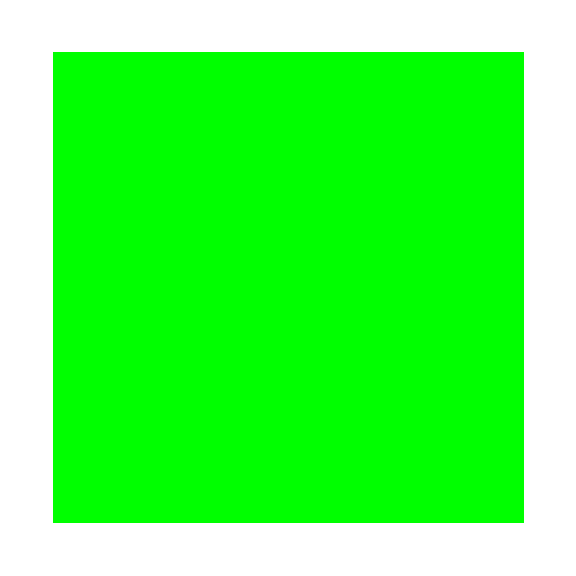

```mathematica
differences=MapThread[Not@*Equal,{CovMatrix50x30tabzSKA[[1]],Transpose[CovMatrix30x50tabzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrix50x30tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixzSKA[[1]],Transpose[MultiSplitCovMatrixzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

## COVARIANCE MATRIX + OCTUPOLE JOINT 10x50

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
CovMatrixOCT50Bx50FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-50B_50F.txt", "Table"], {i,Length[zSKA]}];
CovMatrixOCT30Bx70FzSKA = Table[Import["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d20to160_msplit-40B_60F.txt", "Table"], {i,Length[zSKA]}];
```

```mathematica
CovMatrixOCT50Bx50FzSKA[[1,1,1]]
```

0.0000114066

```mathematica
CovMatrixOCT30Bx70FzSKA[[1,1,1]]
```

0.0000175886

```mathematica
MultiSplitCovMatrixOCTzSKA = Table[
Join[ArrayFlatten[{{CovMatrixOCT50Bx50FzSKA[[i]], CovMatrixOCT50x30tabzSKA[[i]]}}], 
ArrayFlatten[{{CovMatrixOCT30x50tabzSKA[[i]], CovMatrixOCT30Bx70FzSKA[[i]]}}]],
{i,Length[zSKA]}];
```

```mathematica
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,648,648}

```mathematica
MultiSplitCovMatrixOCTzSKA[[All,325;;648,325;;648]]== CovMatrixOCT30Bx70FzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,1;;324,325;;648]]== CovMatrixOCT50x30tabzSKA[[All]]
MultiSplitCovMatrixOCTzSKA[[All,325;;648,1;;324]]== CovMatrixOCT30x50tabzSKA[[All]]
```

True

True

True

```mathematica
SymmetricMatrixQ[CovMatrixOCT50x30tabzSKA[[1]]]
SymmetricMatrixQ[CovMatrixOCT30x50tabzSKA[[1]]]
```

False

False

```mathematica
Table[CovMatrixOCT50x30tabzSKA[[i]] ==CovMatrixOCT30x50tabzSKA[[i]],{i,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

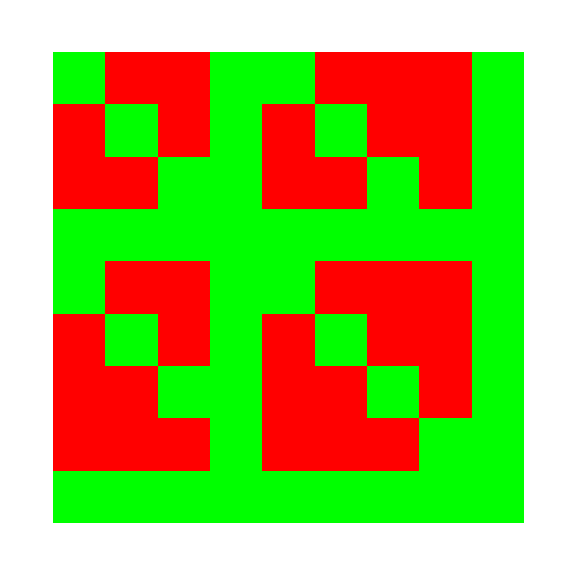

```mathematica
differences=MapThread[Not@*Equal,{CovMatrixOCT50x30tabzSKA[[1]],CovMatrixOCT30x50tabzSKA[[1]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT50x30tabzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[CovMatrixOCT30x50tabzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

```mathematica
SymmetricMatrixQ[MultiSplitCovMatrixOCTzSKA[[1]]]
```

False

```mathematica
differences=MapThread[Not@*Equal,{MultiSplitCovMatrixOCTzSKA[[1]],Transpose[MultiSplitCovMatrixOCTzSKA[[1]]]},2];
ArrayPlot[differences,ColorRules->{True->Red,False->Green}, FrameTicks->{{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None},{Table[{i,If[Mod[i,36]==0,i,""]},{i,Length[MultiSplitCovMatrixOCTzSKA[[1]]]}],None}}, ImageSize->Large  (*Adjust the size as needed*)]
```

-Graphics-

# EXPORT

```mathematica
Dimensions[MultiSplitCovMatrixzSKA]
Dimensions[MultiSplitCovMatrixOCTzSKA]
```

{19,576,576}

{19,648,648}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_all_50x40_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_all_50x40_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",MultiSplitCovMatrixOCTzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
Exit[]
```